## read package

```mathematica
(*SetDirectory["/home/botingw/Downloads"];*)(*other files are under the same directory*)
SetDirectory["/home/sean/Programs/git-repos/physics-research/mathscript"]
<<"pdfParsePDS2013.m"
<<"dtareadbotingw2016.m"
```

/home/sean/Programs/git-repos/physics-research/mathscript

```mathematica
(*global variables*)
(*proton=======================*)

PDISNCl={101,106,169};
PDISNClccbar={147};
PDISNClbbbar={145};
PDISNClqqbar=Flatten[{PDISNClccbar,PDISNClbbbar}];
PDISNC=Flatten[{PDISNCl,PDISNClqqbar}];

PDISCCl1={};
PDISCCl2={};
PDISCC=Flatten[{PDISCCl1,PDISCCl2}];

PVBPZ={204,260,261};(*first 1: pp, left 2: ppbar*)
PVBPW={241,266,267,225,227,234,281};(*first 3: pp, left 4: ppbar*)
PJP={535,538,504,514};(*first 2: pp, left 1: ppbar*)
(*neutron=======================*)

NDISNCl={};
NDISNClqqbar={};
NDISNC=Flatten[{NDISNCl,NDISNClqqbar}];

NDISCCl1={};
NDISCCl2={124,125};
NDISCC=Flatten[{NDISCCl1,NDISCCl2}];

NVBPZ={};
NVBPW={};
NJP={};
(*complex nucleus=======================*)

hDISNCl={102,104};
hDISNClqqbar={};
hDISNC=Flatten[{hDISNCl,hDISNClqqbar}];

hDISCCl1={108,109,110,111};
hDISCCl2={126,127};
hDISCC=Flatten[{hDISCCl1,hDISCCl2}];

hVBPZ={201,203};
hVBPW={};
hJP={};

(*combine types=======================*)
PDISNCCC={159,160};
PVBPWZ={240,268};
```

# Correlation plots project

## data class

## atomic data class

### expinfo class

```mathematica
Exptinfo=
<|
"exptid"->"unset",
"exptname"->"unset",
"feyndiagram"->"unset"
|>
```

<|exptid→unset,exptname→unset,feyndiagram→unset|>

### PDFinfo class

```mathematica
PDFinfo=
<|
"PDFname"->"unset",
"PDFsetmethod"->"unset",
"Nset"->"unset",
"iset"->"unset",
"flavour"->"unset"
|>
```

<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>

### data class

```mathematica
Data=
<|
"label"->"unset",
"data"->"unset"
|>
```

<|label→unset,data→unset|>

## data class specific for .dta data, f(x,Q) data (from .pds), correlation data

### dtadata class

```mathematica
Dtadata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>,
(*2017.01.16 add raw data*)
<|"rawdata"->"unset"|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>,rawdata→unset|>

### fxQdata class

```mathematica
FxQdata=
Join[
Data,
<|
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### fxQsameptdata class

```mathematica
FxQsameptdata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### corrdata class

```mathematica
Corrdata=
Join[
Data,
<|
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### corrsameptdata class

```mathematica
Corrsameptdata=
Join[
Data,
<|
"exptinfo"->Exptinfo,
"PDFinfo"->PDFinfo
|>
]
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

### datamethods class

```mathematica
(*datain={LF[a1__],LF[a2__],...}, dataadd={LF[b1__],LF[b2__],...}, length of two data are the same*)
(*output: {LF[a1__,b1__],LF[a2__,b2__],...}*)
LFadd[datain_,dataaddin_]:=
Module[{data=datain,dataadd=dataaddin,Npt,Nptadd},
Npt=Length[datain];
Nptadd=Length[dataaddin];
If[Npt≠Nptadd,Print["error, #points of data & added data are different"];Return[0] ];
Join[data,dataadd,2]
];

(*pick specific elements in LF*)
(*ex:LFpick[test1,{1,3,5}] output LF[{a}[[1]],{a}[[3]],{a}[[5]] ]*)
LFpick[datain_,picklistin_]:=
Module[{data=datain,picklist=picklistin},
Llist=Length[picklist];
data=data/.LF[a__]:>Apply[LF,Table[{a}[[picklist[[i]] ]],{i,1,Llist}] ];
data
]

(*apply Take rule on all LF elements*)
LFtake[datain_,takelistin_]:=
Module[{data=datain,takelist=takelistin},

data=data/.LF[a__]:>Apply[LF,Take[{a},takelist] ];
data
]

(*apply Delete rule on all LF elements*)
LFdelete[datain_,deletelistin_]:=
Module[{data=datain,deletelist=deletelistin},

data=data/.LF[a__]:>Apply[LF,Delete[{a},deletelist] ];
data
]

(*transf all LF[...] in data to List*)
LFtolist[datain_]:=
Module[{data=datain},

data=data/.LF:>List;
data
]

(*pick columns of data to list*)
(*
ex: LFpicktoList[data,{3,1}] output {x3list,x1list}
x3list = {LF[[3]],LF[[3]],...}, the same for x1list
*)
LFpicktolist[datain_,picklistin_]:=
Module[{data=datain,picklist=picklistin},
Llist=Length[picklist];
data=data/.LF[a__]:>Table[{a}[[picklist[[i]] ]],{i,1,Llist}];
(*transpose from [[Npt,xi]] to [[xi,Npt]] *)
data=Transpose[data,{2,1}];

data
]
```

```mathematica
Datamethods=
<|
"getdatainfo"->
Function[{dataclass},
keys=Keys[dataclass];
Table[
If[keys[[i]]≠ "data",Print[keys[[i]],":\n",dataclass[[keys[[i]] ]] ] ],
{i,1,Length[keys]}]
],
"getdata"->Function[data,data[["data"]] ],
"setdata"->Function[{dataclass,datain},dataclass[["data"]]=datain ],
"getNpt"->Function[data,Length[data[["data"]] ] ],
"getNcolumn"->Function[data,Length[data[["data"]][[1]] ] ],
"getxQ"->"unset",
"getdatalabel"->Function[{dataclass},dataclass[["label"]] ],
"add"->
Function[{dataclassin,dataaddin,labeladdin},
Module[{dataclass=dataclassin,dataadd=dataaddin,labeladd=labeladdin},
(*
If[Dimensions[dataclass[["data"]] ]!=Dimensions[dataadd],Print["error, dimension of data & added data are different"];Return[0] ];
If[Dimensions[dataclass[["label"]] ]!=Dimensions[labeladd],Print["error, dimension of label & added label are different"]Return[0] ];
*)
dataclass[["label"]]=Join[dataclass[["label"]],labeladd];
dataclass[["data"]]=LFadd[dataclass[["data"]],dataadd];
dataclass
(*
dataclass[["label"]]=Join[dataclass[["label"]],labeladd];
dataclass
*)
]
],
"pick"->
Function[{dataclassin,picklistin},
Module[{dataclass=dataclassin,picklist=picklistin},
(*change data*)
dataclass[["data"]]=LFpick[dataclass[["data"]],picklist];
(*change data label, transf Head of it to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFpick[Apply[LF,dataclass[["label"]] ],picklist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"take"->
Function[{dataclassin,takelistin},
Module[{dataclass=dataclassin,takelist=takelistin},
(*change data*)
dataclass[["data"]]=LFtake[dataclass[["data"]],takelist];
(*change data label, transf Head of data label to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFtake[Apply[LF,dataclass[["label"]] ],takelist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"delete"->
Function[{dataclassin,deletelistin},
Module[{dataclass=dataclassin,deletelist=deletelistin},
(*change data*)
dataclass[["data"]]=LFdelete[dataclass[["data"]],deletelist];
(*change data label, transf Head of data label to LF, do the same thing as what you do on data, then transf back to List*)
dataclass[["label"]]=LFdelete[Apply[LF,dataclass[["label"]] ],deletelist];
dataclass[["label"]]=Apply[List,dataclass[["label"]] ];

dataclass
]
],
"tolist"->
Function[{dataclassin},
Module[{dataclass=dataclassin},
(*change data*)
dataclass[["data"]]=dataclass[["data"]]/.LF:>List;

dataclass[["data"]]
]
],(*LFpicktoList[datain_,picklistin_]*)
"picktolist"->
Function[{dataclassin,picklistin},
Module[{dataclass=dataclassin,picklist=picklistin},
(*change data*)
dataclass[["data"]]=LFpicktolist[dataclass[["data"]],picklist];

dataclass[["data"]]
]
],
"reorder"->"unset",
"extract"->"unset",
(*2017.01.16: discard dtaread2016boting`Private` from dtaread2016boting`Private`LF*)
"LFglobal"->
Function[{dataclassin},
Module[{dataclass=dataclassin},
(*change data*)
dataclass[["data"]]=dataclass[["data"]]/.dtaread2016boting`Private`LF ->LF;
dataclass
]
]
|>
```

<|getdatainfo→Function[{dataclass},keys=Keys[dataclass];Table[If[keys⟦i⟧≠data,Print[keys⟦i⟧,:
,dataclass⟦keys⟦i⟧⟧]],{i,1,Length[keys]}]],getdata→Function[data,data⟦data⟧],setdata→Function[{dataclass,datain},dataclass⟦data⟧=datain],getNpt→Function[data,Length[data⟦data⟧]],getNcolumn→Function[data,Length[data⟦data⟧⟦1⟧]],getxQ→unset,getdatalabel→Function[{dataclass},dataclass⟦label⟧],add→Function[{dataclassin,dataaddin,labeladdin},Module[{dataclass=dataclassin,dataadd=dataaddin,labeladd=labeladdin},dataclass⟦label⟧=Join[dataclass⟦label⟧,labeladd];dataclass⟦data⟧=LFadd[dataclass⟦data⟧,dataadd];dataclass]],pick→Function[{dataclassin,picklistin},Module[{dataclass=dataclassin,picklist=picklistin},dataclass⟦data⟧=LFpick[dataclass⟦data⟧,picklist];dataclass⟦label⟧=LFpick[LF@@dataclass⟦label⟧,picklist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],take→Function[{dataclassin,takelistin},Module[{dataclass=dataclassin,takelist=takelistin},dataclass⟦data⟧=LFtake[dataclass⟦data⟧,takelist];dataclass⟦label⟧=LFtake[LF@@dataclass⟦label⟧,takelist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],delete→Function[{dataclassin,deletelistin},Module[{dataclass=dataclassin,deletelist=deletelistin},dataclass⟦data⟧=LFdelete[dataclass⟦data⟧,deletelist];dataclass⟦label⟧=LFdelete[LF@@dataclass⟦label⟧,deletelist];dataclass⟦label⟧=List@@dataclass⟦label⟧;dataclass]],tolist→Function[{dataclassin},Module[{dataclass=dataclassin},dataclass⟦data⟧=dataclass⟦data⟧/.LF:>List;dataclass⟦data⟧]],picktolist→Function[{dataclassin,picklistin},Module[{dataclass=dataclassin,picklist=picklistin},dataclass⟦data⟧=LFpicktolist[dataclass⟦data⟧,picklist];dataclass⟦data⟧]],reorder→unset,extract→unset,LFglobal→Function[{dataclassin},Module[{dataclass=dataclassin},dataclass⟦data⟧=dataclass⟦data⟧/.dtaread2016boting`Private`LF→LF;dataclass]]|>

## .dta data class

## read .dta file into format of dtadata class

### readdtafile class

```mathematica
(*test function: read explist, save exp data with the same exptid into "exptdata"*)
readexptsbydta[dtaDirin_,explistin_]:=
Module[{dtaDir=dtaDirin,explist=explistin,residuetmp,dtafiles,exptdata,Nset,Nexpt},
(*get all .dta files under dtaDir*)
dtafiles=FileNames[dtaDir<>"*dta"];

(*read all data from .dta files*)
residuetmp=
Table[
ReadExptTable[dtafiles[[f]],"ct2016"],
(*
makeobsdataset[ReadExptTable[dtafiles[[f]],"ct2016"],Nexp,"dummy",obs] ,(*//Flatten,*)
*)
{f,1,Length[dtafiles]}
];

Dimensions[residuetmp];
(*
residuetmp[[1,10,7]]
residuetmp[[1,10,7]]/.dtaread2016boting`Private`LF:>List
*)

(*variable to save data we want (in explist)*)
exptdata={};
(*assume #files is the same as Nset*)
Nset=Dimensions[residuetmp][[1]];
Nexpt=Dimensions[residuetmp][[2]];
(*if expt you want in the .dta file, read all iset .dta files into variable "exptdata"*)
Table[
If[
explist[[iexplist]]==residuetmp[[1,iexpt,1]],
Print["find exptid = ",explist[[iexplist]],"." ];
exptdata=Append[exptdata,Table[residuetmp[[iset,iexpt]],{iset,1,Nset}] ] 
];

"dummy"
(*explist[[i]]*)
,{iexplist,1,Length[explist]},{iexpt,1,Nexpt}
];

(*return exp datas with dimensions [[iexpt,iset]]*)
exptdata
]

(*test transf output of ReadExptTable into dtadata class form*)
todtadataclass[datain_,PDFnamein_,PDFsetmethodin_]:=
Module[{data=datain,PDFname=PDFnamein,PDFsetmethod=PDFsetmethodin,Dtadatatmp,Ndatacolumn},
Dtadatatmp=Dtadata;
Dtadatatmp[["data"]]=data[[7]];
Dtadatatmp[["exptinfo","exptid"]]=data[[1]];
Dtadatatmp[["exptinfo","exptname"]]=data[[2]];
Dtadatatmp[["PDFinfo","PDFname"]]=PDFname;
Dtadatatmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;

Dtadatatmp[["label"]]=StringSplit[data[[3]] ];
(*2017.01.19: some labels of expt are not at data[[3]], give them 13 dummy labels, need modify in the future*)
If[
Length[Dtadatatmp[["label"]] ]≠13, 
Ndatacolumn=Length[Apply[List,Dtadatatmp[["data"]][[1]] ] ];(*2017.01.22*)
Dtadatatmp[["label"]]=Table["wrongformat",{i,1,Ndatacolumn}]
];

(*2017.01.16 add dta raw data == utput of ReadExptTable except for it's data *)
Dtadatatmp[["rawdata"]]=Delete[data,7];

Dtadatatmp
]
```

```mathematica
Readdtafile=
<|
"readdta"->readexptsbydta,
"toclass"->todtadataclass
|>
```

<|readdta→readexptsbydta,toclass→todtadataclass|>

## class for operate (edit) dtadata class

### dtaobs class

```mathematica
(*function for calculating residue of dta data*)
addresidue[dataclassin_]:=
Module[{dataclass=dataclassin,ExptID,expItype,residue,NormFac},
ExptID=dataclass[["exptid"]];
expItype=ExptIDinfo[ExptID];

(*get residue method 1*)
(*
residue=data[[7]]/.LF[a__]:>{a}[[13]];
residue=Map[If[#>0,Sqrt[#],-Sqrt[-#]]&,residue,{1}];
*)

(*get residue method 2*)
(*result of method1&2 mostly diff in 5%, method 2 should be accurate*)
(*2017.01.18: NormFac should be in formula or not? with NormFac=1, result of residue is close to "ReducedChi2" *)
NormFac=dataclass[["rawdata"]][[4]];
(*v1*)
(* v1 is wrong
residue=dataclass[["data"]]/.LF[a__]:>LF[({a}[[5]]*NormFac-{a}[[11]])/{a}[[12]] ];
*)
(*v2*)

residue=dataclass[["data"]]/.LF[a__]:>LF[({a}[[5]]-{a}[[11]])/{a}[[12]] ];

dataclass=Datamethods[["add"]][dataclass,residue,{"residue"}];
dataclass
]
```

## .pds data class

## functions in class

### calculate f(x,Q,flavour)

```mathematica
pdflist[xQlistin_,flavourin_,ifamilyin_]:=
Module[{xQlist=xQlistin,flavour=flavourin,ifamily=ifamilyin,x,Q,Nset,output},
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]]] ;(* number of PDF sets *)
output=Table[
x=xQlist[[ix,1]];
Q=xQlist[[ix,2]];
{x,Q,Table[pdfCTEQ[x,Q,flavour,iset],{iset,Nset}]},
{ix,1,Length[xQlist]}
];
output
];

pdfLF[xQLFin_,flavourin_,ifamilyin_]:=
Module[{xQLF=xQLFin,flavour=flavourin,ifamily=ifamilyin,x,Q,Nset,output},
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]]] ;(* number of PDF sets *)
output=Table[
x=xQLF[[ix,1]];
Q=xQLF[[ix,2]];
(*for flavour = {-5,5}, direct use the f(x,Q,flavour)
if it is > 5, we define it's pdf as following:
*)

LF[x,Q,Sequence@@Table[pdfCTEQ[x,Q,flavour,iset],{iset,Nset}] ],
{ix,1,Length[xQLF]}
];
output
];
```

```mathematica
(*input PDFDir, xQLF,PDFsetmethod, and flavour, output FxQdata class*)
fxQcalculate[xQLFin_,PdsDirin_,PDFsetmethodin_,flavourin_]:=
Module[{xQLF=xQLFin,PdsDir=PdsDirin,PDFsetmethod=PDFsetmethodin,flavour=flavourin,fxQclasstmp,ifamily,Nset,datalabel,xQlabel,PDFname},
fxQclasstmp=FxQdata;

(*setup pdf function*)
pdfResetCTEQ;
(*
For[i=1,i≤20,i++,pdfFamilyParseCTEQ["Dummy"]];
*)
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
pdfFamilyParseCTEQ[PdsDir<>"*pds",ifamily];

Nset=Length[pdfSetList[[ifamily]] ];(* number of PDF sets *)
(*set data label*)
datalabel=Table[ToString[i-1],{i,1,Nset}];
xQlabel={"x","Q"};
datalabel=Join[xQlabel,datalabel];
(*set PDFname*)
PDFname=StringSplit[PdsDir,"/"][[-1]];
(*set info of class*)
fxQclasstmp[["label"]]=datalabel;
fxQclasstmp[["PDFinfo","PDFname"]]=PDFname;
fxQclasstmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
fxQclasstmp[["PDFinfo","Nset"]]=Nset;
fxQclasstmp[["PDFinfo","flavour"]]=flavour;
(*calculate data by xQ*)
fxQclasstmp[["data"]]=pdfLF[xQLF,flavour,ifamily];
(*output*)
fxQclasstmp

];
```

### calculate f(x,Q,flavour) by same point of experiments (from dtadata class)

```mathematica
(*read xQLF from Dtadata, pds file from PdsDir and set flavour
output FxQsameptdata class, 
"exptinfo" is copy from Dtadata[["exptinfo"]], "PDFinfo" is set by input parameter *)
fxQsameptcalculate[dtadataclassin_,PdsDirin_,PDFsetmethodin_,flavourin_]:=
Module[{dtadataclass=dtadataclassin,PdsDir=PdsDirin,PDFsetmethod=PDFsetmethodin,flavour=flavourin,fxQclasstmp},
fxQclasstmp=FxQsameptdata;

(*2017,01,12*)
(*here we do not deal with part: extract {x,Q} from dtadata, this part need modified later.  *)
fxQclasstmp=fxQcalculate[dtadataclass[["data"]],PdsDir,PDFsetmethod,flavour];
fxQclasstmp[["exptinfo"]]=dtadataclass[["exptinfo"]];
fxQclasstmp
]
```

```mathematica
(*input fxQdataclass[[flavour]], flavour from -5 ~ 5, output the customized f(x,Q), as following:
dbar/ubar, d/u, s+sbar/ubar+dbar
*)
(*the way to calculate the combination of pdf could be modify: if f(x,Q,flavour)=0, then don't consider the point*)


setextrafxQ[fxQdataclasslistin_]:=
Module[{fxQdataclasslist=fxQdataclasslistin,bbar,cbar,sbar,dbar,ubar,g,u,d,s,c,b,Npt,Nset,newfxQdata,LFa,LFb,LFc,LFd,x,Q,Nsetdata,fxQmincut,dbarubar,du,ssbarubardbar},
(*set quark label*)
{bbar,cbar,sbar,dbar,ubar,g,u,d,s,c,b}={-5+6,-4+6,-3+6,-2+6,-1+6,0+6,1+6,2+6,3+6,4+6,5+6};
(*set variables, assume all of fxQdataclasslist have the same Npt, label*)
Npt=Datamethods[["getNpt"]][fxQdataclasslist[[1]] ];
Nset=Datamethods[["getNcolumn"]][fxQdataclasslist[[1]] ]-2;
(*pdf minimum cut for denominator*)
fxQmincut=10.0^-10;
(*set classes for newly defined flavours*)
dbarubar=fxQdataclasslist[[1]];
du=fxQdataclasslist[[1]];
ssbarubardbar=fxQdataclasslist[[1]];

(*dbar/ubar*)
LFa=fxQdataclasslist[[dbar]][["data"]];
LFb=fxQdataclasslist[[ubar]][["data"]];

dbarubar[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0, 
LFa[[ix,iset+2]]/Max[LFb[[ix,iset+2]],fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

(*d/u*)
LFa=fxQdataclasslist[[d]][["data"]];
LFb=fxQdataclasslist[[u]][["data"]];

du[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0, 
LFa[[ix,iset+2]]/Max[LFb[[ix,iset+2]],fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

(*s+sbar/ubar+dbar*)
LFa=fxQdataclasslist[[s]][["data"]];
LFb=fxQdataclasslist[[sbar]][["data"]];
LFc=fxQdataclasslist[[ubar]][["data"]];
LFd=fxQdataclasslist[[dbar]][["data"]];

ssbarubardbar[["data"]]=
Table[
x=LFa[[ix,1]];Q=LFa[[ix,2]];
Nsetdata=
Table[
If[
LFa[[ix,iset+2]]≠0 && LFb[[ix,iset+2]]≠0&& LFc[[ix,iset+2]]≠0&& LFd[[ix,iset+2]]≠0, 
(LFa[[ix,iset+2]]+LFb[[ix,iset+2]])/Max[(LFc[[ix,iset+2]]+LFd[[ix,iset+2]]),fxQmincut],
0.0
],
{iset,1,Nset}
];
LF[x,Q,Sequence@@Nsetdata],
{ix,1,Npt}
];

{dbarubar,du,ssbarubardbar}
]
```

## read .pds file into format of fxQdata(fxQsameptdata) class

### pdsread class

```mathematica
Pdsread=
<|
"fxQ"->fxQcalculate,
"fxQsamept"->fxQsameptcalculate
|>
```

<|fxQ→fxQcalculate,fxQsamept→fxQsameptcalculate|>

## correlation data class

## calculate correlation function (general version) input any two observables, get correlation

### corrcalculate class

```mathematica
(*input: obsALF={LF[N elements],...}, obsBLF: same as obsALF*)
(*output list of correlation: {corr1,corr2,corr3,......}*)
(*2017.01.12 not yet consider MC correlation part*)
corrAB[obsALFin_,obsBLFin_]:=
Module[{obsALF=obsALFin,obsBLF=obsBLFin,NA,NB,NptA,NptB,Npt,correlation},
NA=Length[obsALF[[1]] ];
NB=Length[obsBLF[[1]] ];
If[NA≠NB,Print["error, two observables has different length"];Return[0] ];
(*# of points*)
NptA=Length[obsALF];
NptB=Length[obsALF];
If[NptA≠NptB,Print["error, two observables has different #points"];Return[0] ];
Npt=NptA;

(*calculate correlation for all points*)
correlation=Table[
pdfHessianCorrelation[obsALF[[ix]]/.LF->List,obsBLF[[ix]]/.LF->List],
{ix,1,Npt}];
(*output the list of correlation for all points*)
correlation
];
```

## calculate correlation function (specific for corr(f(x,Q,flavour), obs(x,Q)), obs==residue, deltaR*residue) and LF[x,Q,deltaR] data, they are for plots of default

### corrfxQresiduesamept class

```mathematica
(*input a dtadata class with data=={LF[x,Q,obs1,obs2,...obsNset],...}
and a fxQsameptdata class with data=={LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...},
the function assume {x,Q} of dtadataclass & fxQsameptdataclass are the same
output the corrsameptdata class*)
corrfxQdtaobs[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{dtadataclass=dtadataclassin,fxQsameptdataclass=fxQsameptdataclassin,corrsameptdatatmp,obsALF,obsBLF,corrdatatmp,Npt,x,Q},
(*set info part of output class*)
corrsameptdatatmp=Corrsameptdata;
corrsameptdatatmp[["exptinfo"]]=dtadataclass[["exptinfo"]];
corrsameptdatatmp[["PDFinfo"]]=dtadataclass[["PDFinfo"]];
(*set f(x,Q) data (delete x,Q part of data)*)
obsALF=LFdelete[fxQsameptdataclass[["data"]],{{1},{2}}];
(*set obs data*)
obsBLF=LFdelete[dtadataclass[["data"]],{{1},{2}}];

(*calculate correlation*)
corrdatatmp=corrAB[obsALF,obsBLF];
(*{corr(x1,Q1),...}->{LF[x,Q,corr(x1,Q1)]}*)
Npt=Length[obsALF];
corrdatatmp=
Table[
(*assume {x,Q} of dtadataclass & fxQsameptdataclass are the same*)
x=dtadataclass[["data"]][[ix,1]];
Q=dtadataclass[["data"]][[ix,2]];
LF[x,Q,corrdatatmp[[ix]] ]
,
{ix,1,Npt}
];

corrsameptdatatmp[["data"]]=corrdatatmp;
corrsameptdatatmp[["label"]]={"x","Q","corr"};
(*output*)
corrsameptdatatmp
(*
{obsALF,obsBLF,corrdatatmp}
*)
];
```

```mathematica
(*input a dtadata class with data=={LF[x,Q,obs1,obs2,...obsNset],...}
and a fxQsameptdata class with data=={LF[x,Q,f(x,Q,flavour,iset1),...,f(x,Q,flavour,Nset)],...},
the function assume {x,Q} of dtadataclass & fxQsameptdataclass are the same
output the corrsameptdata class with dr*)
dRcorrfxQdtaobs[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{dtadataclass=dtadataclassin,fxQsameptdataclass=fxQsameptdataclassin,deltaR,Npt,Nset,output,drcorrtmp},

deltaR=getdeltaR[dtadataclass];
Npt=Datamethods[["getNpt"]][dtadataclass];
Nset=Datamethods[["getNcolumn"]][dtadataclass]-2;(*Ncolumn = Nset + 2 (x&Q)*)

drcorrtmp=corrfxQdtaobs[dtadataclass,fxQsameptdataclass];
(*calculate dr*corr for all points*)
Table[
drcorrtmp[["data"]][[ix,3]]=drcorrtmp[["data"]][[ix,3]]*deltaR[[ix]],
{ix,1,Npt}
];

drcorrtmp
]
```

```mathematica
corrfxQdtaresidue[dtadataclassin_,fxQsameptdataclassin_]:=
Module[{},
"testoutput"
]
```

```mathematica
(*input a class with LF[x,Q,iset1,...,Nset]*)
(*output deltaR as List: {dR1,dR2,...dR Npt}*)
getdeltaR[dtadataclassin_]:=
Module[{dtadataclass=dtadataclassin,Npt,observable,deltaR,PDFerror1},
Npt=Datamethods[["getNpt"]][dtadataclass];
(*take Nset of observables (delete x,Q)*)
(*{LF[iset,...,Nset],...}*)
observable=Datamethods[["take"]][dtadataclass,{3,-1}];
observable=Datamethods[["tolist"]][observable];

deltaR=
Table[
PDFerror1= Max[pdfHessianSymError[observable[[ix]] ], 10^-8],
{ix,1,Npt}];
deltaR
]


getdeltaRclass[dtadataclassin_]:=
Module[{dtadataclass=dtadataclassin,Npt,observable,deltaR,PDFerror1},
Npt=Datamethods[["getNpt"]][dtadataclass];
(*take Nset of observables (delete x,Q)*)
(*{LF[iset,...,Nset],...}*)
observable=Datamethods[["take"]][dtadataclass,{1,2}];
deltaR=getdeltaR[dtadataclass];
(*transf to {LF[],LF[],...}*)
deltaR=
Table[LF[deltaR[[ix]] ],{ix,1,Npt}];

(*{x,Q} + {deltaR}*)
observable=Datamethods[["add"]][observable,deltaR,{"deltaR"}];

observable
]
```

```mathematica
corrfxQresiduesamept=
<|
"corrsamept"->corrfxQdtaobs,
"dRcorrsamept"->dRcorrfxQdtaobs,
"deltaR"->getdeltaR,
"residue"->corrfxQdtaresidue
|>
```

<|corrsamept→corrfxQdtaobs,dRcorrsamept→dRcorrfxQdtaobs,deltaR→getdeltaR,residue→corrfxQdtaresidue|>

## read/write class

## IO of a general data class

### IO number transform: always transform a number into scientific notation

```mathematica
(*show a number to scientific form: ex: 312.5 -> 3.125E2*)
ToSciForm[N_,decimal_]:=
Module[{output},
output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E",#3}]&)];
(*case: if becom N1E, it means N1E0, ex: 3.55E means 3.55*10^0 = 3.55E0*)
If[Length[StringSplit[ToString[output],"E"] ] ==1,output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E","0"}]&)] ];
(*case of 0, it will transf to 0E, so we need to modify to 0E0*)
(*
If[N==0 || (Abs[N]≥1 && Abs[N]<10),output=ScientificForm[N,decimal,NumberFormat->(Row[{#1,"E","0"}]&)] ];
*)
output
]

(*transf a string of scientific notation to number, ex: "3.125E2" -> 312.5*)
(*mathematica could not transf it, *)
SciStrToNumber[str_]:=
Module[{strtmp},
strtmp=StringSplit[str,"E"];
If[Length[strtmp]≠2,Print["error, input is not a number with scientific notation, ",str] ];
ToExpression[strtmp[[1]]<>"*"<>"10^"<>strtmp[[2]] ]
]
```

### write data class

### read data class

## IO of fxQdata class

```mathematica
(*fxQ format for IO:
pdfflavours[[#flavour]][[Npt]][[ x, Q, {#iset of pdf(x,Q)}]]
*)
```

### write fxQdata class

```mathematica
(*input data format: {LF[x,Q,iset,...,Nset],LF[],...}, transform it's data to format of IO (used by function pdfwritesameptnew)*)
LFtoIOformat[datain_]:=
Module[{data=datain,output},
output=data/.LF[a__]:>{{a}[[1]],{a}[[2]],Take[{a},{3,-1}]};
output
]

IOtoLFformat[datain_]:=
Module[{data=datain,Npt,Nset,fmax,x,Q,output},

Npt=Length[data];
output=
Table[
(*x and Q*)
x=data[[ix,1]];Q=data[[ix,2]];
LF[x,Q,Sequence@@data[[ix,3]] ],
{ix,1,Npt}
];

output
]
(*input a IO (used by function pdfwritesameptnew), transform it's data to format of fxQclass*)
(*
IOtofxQclassformat[pdfflavoursin_,exptidin_,exptnamein_,PDFnamein_,PDFsetmethodin_,flavourin_]:=
Module[{pdfflavours=pdfflavoursin,Npt,Nset,fmax,x,Q,output},
(*set variables*)
Npt=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt,fmax,Nset}];

output=FxQsameptdata;
(*set info*)
output[["label"]]=Join[{"x","Q"},Table[ToString[i],{i,1,Nset}] ];
output[["exptinfo","exptid"]]=exptid;
output[["exptinfo","exptname"]]=exptname;
output[["PDFinfo","PDFname"]]=PDFname;
output[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
output[["PDFinfo","Nset"]]=Nset;
output[["PDFinfo","flavour"]]=flavour;

output[["data"]]=
Table[
Table[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
LF[x,Q,Sequence@@pdfflavours[[f+6,ix,3]] ],
{ix,1,Npt}
],
{f,-5,-5+fmax-1}
];



output
]
*)
```

```mathematica
FxQsameptdata
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

```mathematica
(*PDFCorrelationplot[MyCorrelations,"corr g-chi","x","Q",{0.00001,1,1,120},0.2,0.2]*)
(*observablein: {{ {x,Q}, {obs1,obs2,...obs(iset)}}, { {x,Q}, {obs1,obs2,...obs(iset)}},...}*)
(*datafilein: filename used to store data*)
(*IO test, scientific in/output format not supported by mathematica, we can use NumberForm to control output precision *)
pdfwritesamept[observablein_,ifamilyin_,datafilein_]:=
Module[{observable=observablein,ifamily=ifamilyin,datafile=datafilein,xQlist,pdfflavours,x,Q,MyCorrelations,str,Nset,Nset2,xQstr,pdfisetstr,fmax,outputprecision},

(*extract (x,Q) value from observable*)
xQlist=Flatten[Take[observable,All,1],1];

(*set #iset*)
pdfSetActiveFamily[ifamily]; (* choose PDF family *)
Nset=Length[pdfSetList[[ifamily]] ] ;(* number of PDF sets *)
Nset2=Length[observable[[1,2]] ];
If[Nset≠Nset2,Print["error, info of #iset in observable and ifamily are different"]];
(*set fmax*)
fmax=11;


(*generate pdf value for all flavour, (x,Q) points*)

pdfflavours=
Table[Print["calculate pdf ",flavour];pdflist[xQlist,flavour,1],{flavour,-5,5}];(*test mode: run fast*)

(*open write*)
str=OpenWrite[datafile];

WriteString[str,"#flavour: "<>ToString[fmax]<>"  Npt: "<>ToString[Length[xQlist] ]<>" #iset: "<>ToString[Nset]<> "\n"];


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=xQlist[[ix,1]];Q=xQlist[[ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Length[xQlist]}
];,
{f,-5,5}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];

pdfwritesameptnew[pdfflavoursin_,datafilein_]:=
Module[{pdfflavours=pdfflavoursin,datafile=datafilein,x,Q,str,Npt,Nset,Nset2,xQstr,pdfisetstr,fmax,outputprecision},

(*set variables*)
Npt=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt,fmax,Nset}];


(*open write*)
str=OpenWrite[datafile];

WriteString[str,"#flavour: "<>ToString[fmax]<>"  Npt: "<>ToString[Npt]<>" #iset: "<>ToString[Nset]<> "\n"];


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];

(*input: dataclasslist: FxQsameptdata[[flavour]]*)
(*save f(x,Q,flavour) into file*)
pdfwritesamept2new[dataclasslistin_,datafilein_]:=
Module[{dataclasslist=dataclasslistin,datafile=datafilein,pdfflavours,x,Q,str,Npt,Npt2,Nset,Nset2,xQstr,pdfisetstr,fmax,fmax2,outputprecision,exptid,exptname,PDFname,PDFsetmethod},

(*transform data format*)
Npt=Datamethods[["getNpt"]][dataclasslist[[1]] ];
fmax=Length[dataclasslist];(*how many f(x,Q,flavour) input*)
Nset=Datamethods[["getNcolumn"]][dataclasslist[[1]] ]-2;

pdfflavours=
Table[
LFtoIOformat[dataclasslist[[f+6]][["data"]] ],
{f,-5,-5+fmax-1}
];

(*set variables*)
Npt2=Length[pdfflavours[[1]] ];(*assume all points have the same points, it could be modified to Npt(flavour)*)
fmax2=Length[pdfflavours];(*how many f(x,Q,flavour) input*)
Nset2=Length[pdfflavours[[1,1,3]] ];(*Nset*)
(*test*)Print["{Npt,fmax,Nset} = ",{Npt2,fmax2,Nset2}];

(*check if diff from the info on class*)
If[Npt2≠Npt,Print["error, #Npt "] ];
If[fmax2≠fmax,Print["error, #flavour"] ];
If[Nset2≠Nset,Print["error, Nset"] ];

(*set data info*)
exptid=dataclasslist[[1]][["exptinfo","exptid"]];
exptname=dataclasslist[[1]][["exptinfo","exptname"]];
PDFname=dataclasslist[[1]][["PDFinfo","PDFname"]];
PDFsetmethod=dataclasslist[[1]][["PDFinfo","PDFsetmethod"]];

(*open write*)
str=OpenWrite[datafile];

WriteString[
str,
"#flavour: "<>ToString[fmax]<>
"  Npt: "<>ToString[Npt]<>
" #iset: "<>ToString[Nset]<> 
" #exptid: "<>ToString[exptid]<>
" exptname: "<>exptname<>
" PDFname: "<>PDFname<>
" PDFsetmethod: "<>PDFsetmethod<>
"\n"
];
(*
output[["exptinfo","exptid"]]=exptid;
output[["exptinfo","exptname"]]=exptname;
output[["PDFinfo","PDFname"]]=PDFname;
output[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
output[["PDFinfo","Nset"]]=Nset;
output[["PDFinfo","flavour"]]=flavour;
*)


Do[
WriteLine[str,"flavour= "<>ToString[f] ];
Do[
(*x and Q*)
x=pdfflavours[[f+6,ix,1]];Q=pdfflavours[[f+6,ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
(*f(x,Q) for all iset*)
pdfisetstr="";(*ToString > StringJoin*)

outputprecision=10;
(*
pdfisetstr=ToString[#]&/@NumberForm[pdfflavours[[f+6,ix,3]],outputprecision ];
pdfisetstr=ToString[NumberForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
*)
pdfisetstr=ToString[ToSciForm[#,outputprecision]]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];

,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}
];


Close[str];

(*
pdfflavours
*)
{1,1,1}
];
```

### read fxQdata class

```mathematica
(*read data stored by function pdfwritesamept*)
(*read info of {fmax,Npt,Nset}, then check whether data is the same as {fmax,Npt,Nset}, if yes -> output the data by
observablein: {{ {x,Q}, {obs1,obs2,...obs(iset)}}, { {x,Q}, {obs1,obs2,...obs(iset)}},...}
where {fmax,Npt,Nset} means #flavour in data, #of points of data, #iset of data*)
(*output format:
pdfflavours[[#flavour]][[Npt]][[ x, Q, {#iset of pdf(x,Q)}]]
*)
pdfreadsamept2[datafilein_]:=
Module[{datafile=datafilein,xQlist,pdfflavours,pdfisetstr,x,Q,MyCorrelations,str,fmax,fmax2,Npt,dummy,i,Nset,mystr,tmpdata,exptid,exptname,PDFname,PDFsetmethod,outputtmp,output},

(*open file*)
str=OpenRead[datafile];
(*read info {fmax,Npt,Nset} from first line of file*)
{dummy,fmax,dummy,Npt,dummy,Nset,dummy,exptid,dummy,exptname,dummy,PDFname,dummy,PDFsetmethod}=
Read[str,{Word,Number,Word,Number,Word,Number,Word,Number,Word,Word,Word,Word,Word,Word}];
Print["{#flavour, Npt, #set} = ",{fmax,Npt,Nset,exptid,exptname,PDFname,PDFsetmethod}];
(*dummy=ReadLine[str];Print[dummy];*)(*read left of the line*)

(*seperate flavour data to a list*)
tmpdata=ReadList[str,Record,RecordSeparators->"flavour="];
tmpdata=Drop[tmpdata,1];(*first element is dummy*)
fmax2=Length[tmpdata];
If[fmax≠fmax2,Print["error, head info of total #flavour inconsistent with data, fmax1: ",fmax," fmax2: ",fmax2 ];Return["error"] ];

mystr=Table[StringToStream[tmpdata[[f]] ],{f,1,fmax2}];

Close[str];

(*declare variable*)
pdfflavours={};
dummy={};
x={};
Q={};
pdfisetstr={};

(*read data from file to pdfflavours*)
Do[
(*
dummy=ReadLine[mystr[[f+6]] ];
*)

dummy=Read[mystr[[f+6]],Number];(*read flavour index*)
pdfflavours=Append[pdfflavours,{}];

Do[
(*x and Q*)
x=Read[mystr[[f+6]],Number];
Q=Read[mystr[[f+6]],Number];

(*Nset=57;*)
(*
pdfisetstr=Read[mystr[[f+6]],Table[Number,{i,1,Nset}] ];
*)
pdfisetstr=Read[mystr[[f+6]],Table[Word,{i,1,Nset}] ];(*scientific notation-> word-> number*)
pdfisetstr=SciStrToNumber[#]&/@pdfisetstr;(*word-> number array*)

(*read left part of last line*)
dummy=ReadLine[mystr[[f+6]] ];

(*set {x,Q,{#iset of pdf}} of ix *)
pdfflavours[[f+6]]=Append[pdfflavours[[f+6]],{}];
pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],x];
pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],Q];

pdfflavours[[f+6,ix]]=Append[pdfflavours[[f+6,ix]],pdfisetstr];

(*
x=xQlist[[ix,1]];Q=xQlist[[ix,2]];
xQstr=ToString[x]<>" "<>ToString[Q];
*)
(*f(x,Q) for all iset*)
(*
pdfisetstr="";(*ToString > StringJoin*)

pdfisetstr=ToString[#]&/@pdfflavours[[f+6,ix,3]];
pdfisetstr=StringJoin[#," "]&/@pdfisetstr;
pdfisetstr=StringJoin[pdfisetstr];

WriteLine[str,xQstr];
WriteLine[str,pdfisetstr];
*)
,
{ix,1,Npt}
];,
{f,-5,-5+fmax-1}(*test f*)
];

(*set data*)
output=
Table[
(*set fxQdataclass*)
outputtmp=FxQsameptdata;
(*set info*)
outputtmp[["label"]]=Join[{"x","Q"},Table[ToString[i],{i,1,Nset}] ];
outputtmp[["exptinfo","exptid"]]=exptid;
outputtmp[["exptinfo","exptname"]]=exptname;
outputtmp[["PDFinfo","PDFname"]]=PDFname;
outputtmp[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
outputtmp[["PDFinfo","Nset"]]=Nset;
(*output[["PDFinfo","flavour"]]=flavour;*)

(*set data*)
outputtmp[["data"]]=IOtoLFformat[pdfflavours[[f+6]] ];
(*output*)
outputtmp,
{f,-5,-5+fmax-1}
];

output
]
```

## IO of corrdata class

### write corrdata class

### read corrdata class

## IO of config file

```mathematica
(*write config file*)
makecorrconfigfile[configDirin_,configfilenamein_,figureDirin_,myPDFsetDirin_,PDFsetmethodin_,PDFnamein_,PDFDataDirin_,datalistFilein_,expttypein_,exptidin_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,figureDir=figureDirin,myPDFsetDir=myPDFsetDirin,PDFsetmethod=PDFsetmethodin,PDFname=PDFnamein,PDFDataDir=PDFDataDirin,datalistFile=datalistFilein,expttype=expttypein,exptid=exptidin,figureDirtag,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,expttypetag,exptidtag,
figureDirtext,PDFsetDirtext,PDFsetmethodtext,PDFDataDirtext,CorrDataDirtext,PDFnametext,datalistFiletext,expttypetext,exptidtext,
s,enterstr,exptidtmp},
(*set tag of arguments*)
figureDirtag=" = figureDirtag !";

PDFsetDirtag=" = PDFsetDir !";
PDFsetmethodtag=" = PDFsetmethod !";

PDFDataDirtag=" = PDFDataDir !";
CorrDataDirtag=" = CorrDataDir !";
PDFnametag=" = PDFname !";

datalistFiletag=" = datalist !";

expttypetag=" = expttype !";
exptidtag=" = exptid !";
(*set text for explanation of arguments*)
figureDirtext=" the directory used to save figure files";

PDFsetDirtext="  PDFset directory ";
PDFsetmethodtext="  method used to generate PDFset ";

PDFDataDirtext="  directory storing f(x,Q) data ";
CorrDataDirtext="  directory storing correlation data ";
PDFnametext="  PDFname of file storing f(x,Q) value ";

datalistFiletext="  datalist with experimental information ";

expttypetext="  expt type mode: single, multi, All, ProtonNeutron are available options ";
exptidtext="  experimental ID ";

enterstr="\n";

s=OpenWrite[configDir<>configfilename];
WriteString[s,"#this file is config file of correlation_plot_project_v3.nb\n"];
WriteString[s,"#figureDir is the directory of figure files \n"];
WriteString[s,"#PDFsetDir is the directory of PDFset, PDFsetmethod = Hessian or MC \n"];
WriteString[s,"#PDFDataDir is directory store f(x,Q) data, PDFname is name of PDFset, ex: CT14NNLO \n"];
WriteString[s,"#datalistFile is the file with experimental information \n"];
WriteString[s,"#expttype & exptid are used to decide which experiments you want to show  \n"];
WriteString[s,"\n"];

WriteString[s,figureDir,figureDirtag,figureDirtext,enterstr];
WriteString[s,"\n"];

WriteString[s,myPDFsetDir,PDFsetDirtag,PDFsetDirtext,enterstr];
WriteString[s,PDFsetmethod,PDFsetmethodtag,PDFsetmethodtext,enterstr];
WriteString[s,"\n"];

WriteString[s,PDFDataDir,PDFDataDirtag,PDFDataDirtext,enterstr];
(*WriteString[s,CorrDataDir,CorrDataDirtag,CorrDataDirtext,enterstr];*)
WriteString[s,PDFname,PDFnametag,PDFnametext,enterstr];
WriteString[s,"\n"];

WriteString[s,datalistFile,datalistFiletag,datalistFiletext,enterstr];
WriteString[s,"\n"];

WriteString[s,expttype,expttypetag,expttypetext,enterstr];
WriteString[s,"\n"];
(*if single or multi type, save format = #1 #2 #3 ... = xxx! *)
exptidtmp="";(*initialize exptidtmp, exptidtmp is a string with format of expid in the config file*)
If[
expttype=="All" || expttype=="ProtonNeutron",
exptidtmp=exptid
];
If[
expttype=="single" || expttype=="multi",
exptidtmp=Table[ToString[exptid[[iexptid]] ]<>" ",{iexptid,1,Length[exptid]}];
exptidtmp=StringJoin[exptidtmp];
exptidtmp=Drop[exptidtmp,-1];(*drop the last " "*)
];
WriteString[s,exptidtmp,exptidtag,exptidtext,enterstr];
WriteString[s,"\n"];
(*
If[
StringContainsQ[output[[i]],exptidtag] && (expttype=="single" || expttype=="multi"),
exptidtmp=ReadList[StringToStream[output[[i]] ],Record,RecordSeparators->exptidtag];
If[Length[exptidtmp]==2,exptid=ReadList[StringToStream[exptidtmp[[1]] ],Number] ](*structure is like exptid... exptidtag explanation, so exptidtmp = 2 *)
];
*)

Close[s];

"make correlation config file done"
]


(*
makecorrconfigfile[configDirin_,configfilenamein_,myPDFsetDirin_,PDFsetmethodin_,PDFnamein_,PDFDataDirin_,datalistFilein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,myPDFsetDir=myPDFsetDirin,PDFsetmethod=PDFsetmethodin,PDFname=PDFnamein,PDFDataDir=PDFDataDirin,datalistFile=datalistFilein,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,s.enterstr},

PDFsetDirtag=" = PDFset directory !";
PDFsetmethodtag=" = method used to generate PDFset !";

PDFDataDirtag=" = directory storing f(x,Q) data !";
CorrDataDirtag=" = directory storing correlation data !";
PDFnametag=" = PDFname of file storing f(x,Q) value !";

datalistFiletag=" = datalist with experimental information !";

s=OpenWrite[configDir<>configfilename];
WriteString[s,"#this file is config file of correlation_plot_project_v3.nb\n"];
WriteString[s,"#PDFsetDir is the directory of PDFset, PDFsetmethod = Hessian or MC \n"];
WriteString[s,"#PDFDataDir is directory store f(x,Q) data, PDFname is name of PDFset, ex: CT14NNLO \n"];
WriteString[s,"#datalistFile is the file with experimental information \n"];
WriteString[s,"\n"];

enterstr="\n";
WriteString[s,myPDFsetDir,PDFsetDirtag,enterstr];
WriteString[s,PDFsetmethod,PDFsetmethodtag,enterstr];
WriteString[s,"\n"];

WriteString[s,PDFDataDir,PDFDataDirtag,enterstr];
WriteString[s,CorrDataDir,CorrDataDirtag,enterstr];
WriteString[s,PDFname,PDFnametag,enterstr];
WriteString[s,"\n"];

WriteString[s,datalistFile,datalistFiletag,enterstr];

Close[s];

"make correlation config file done"
]
*)
```

```mathematica
(*read config file*)
(*script version, add runfunc mode into configure file, so that user can use commands to decide which function he want to run*)
readcorrconfigfile[configDirin_,configfilenamein_]:=
Module[{configDir=configDirin,configfilename=configfilenamein,
runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,CorrDataDir,datalistFile,expttype,exptid,
runfunctag,figureDirtag,PDFsetDirtag,PDFsetmethodtag,PDFDataDirtag,CorrDataDirtag,PDFnametag,datalistFiletag,expttypetag,exptidtag,
runfunctext,figureDirtext,PDFsetDirtext,PDFsetmethodtext,PDFDataDirtext,CorrDataDirtext,PDFnametext,datalistFiletext,expttypetext,exptidtext,
s,output,exptidtmp},
(*set tag of arguments*)
runfunctag=" = runfunc !";
figureDirtag=" = figureDirtag !";

PDFsetDirtag=" = PDFsetDir !";
PDFsetmethodtag=" = PDFsetmethod !";

PDFDataDirtag=" = PDFDataDir !";
CorrDataDirtag=" = CorrDataDir !";
PDFnametag=" = PDFname !";

datalistFiletag=" = datalist !";

expttypetag=" = expttype !";
exptidtag=" = exptid !";

(*set text for explanation of arguments*)
runfunctext=" the action you want to do, what you can do: save_fx, save_corr_plots";
figureDirtext=" the directory used to save figure files";

PDFsetDirtext="  PDFset directory ";
PDFsetmethodtext="  method used to generate PDFset ";

PDFDataDirtext="  directory storing f(x,Q) data ";
CorrDataDirtext="  directory storing correlation data ";
PDFnametext="  PDFname of file storing f(x,Q) value ";

datalistFiletext="  datalist with experimental information ";

expttypetext="  expt type mode: single, multi, All, ProtonNeutron are available options ";
exptidtext="  experimental ID ";

(*tag of arguments*)
(*
PDFsetDirtag=" = PDFset directory !";
PDFsetmethodtag=" = method used to generate PDFset !";

PDFDataDirtag=" = directory storing f(x,Q) data !";
CorrDataDirtag=" = directory storing correlation data !";
PDFnametag=" = PDFname of file storing f(x,Q) value !";

datalistFiletag=" = datalist with experimental information !";
*)
(*initialize arguments*)
runfunc="unset";
figureDir="unset";
myPDFsetDir="unset";
PDFsetmethod="unset";
PDFname="unset";
PDFDataDir="unset";
datalistFile="unset";
expttype="unset";
exptid="unset";

(*read file*)
s=OpenRead[configDir<>configfilename];
output=ReadList[s,String];
Close[s];

(*if read tag, assign the first word of that line to arguments*)
Table[
If[
StringContainsQ[output[[i]],runfunctag],
runfunc=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],figureDirtag],
figureDir=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],PDFsetDirtag],
myPDFsetDir=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],PDFsetmethodtag],
PDFsetmethod=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],PDFDataDirtag],
PDFDataDir=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],CorrDataDirtag],
CorrDataDir=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],PDFnametag],
PDFname=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],datalistFiletag],
datalistFile=Read[StringToStream[output[[i]] ],Word]
];
If[
StringContainsQ[output[[i]],expttypetag],
expttype=Read[StringToStream[output[[i]] ],Word]
];
(*read exptid, assuming there are several exptids*)
(*take string in front of exptidtag, then read all numbers from string*)
If[
StringContainsQ[output[[i]],exptidtag] && (expttype=="single" || expttype=="multi"),
exptidtmp=ReadList[StringToStream[output[[i]] ],Record,RecordSeparators->exptidtag];
If[Length[exptidtmp]==2,exptid=ReadList[StringToStream[exptidtmp[[1]] ],Number] ](*structure is like exptid... exptidtag explanation, so exptidtmp = 2 *)
];
(*don't need to set exptid if expttype = All,ProtonNeutron*)
"dummy"
,{i,1,Length[output]}
];

(*if any arguments still unset, return error message*)
(*output the config setting*)
{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid}
]
```

## plot class

## print function: print info of experiment in a PDFset

```mathematica
printprocessbyPDFset[pdfsetfilein_,datalistFilein_]:=
Module[{pdfsetfile=pdfsetfilein,datalistFile=datalistFilein,processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle},
(*set processes title, expid*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};

PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
(*PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";*)
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";

processestitle={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle};

(*call datalist with experimental information*)
(*datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";*)
(*datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";*)
ReadLisFile[datalistFile];
(*
ExptIDtoName[124] ;
ExptList1=(*ReadExptTable[DtaDir<>"If135r.00.dta","ct2016"];*)ReadExptTable[CT14NNLODtaDir<>"CT14nn.00.dta","ct2016"];
*)

(*get information of experiments in the PDFset we choose*)
ExptList1=ReadExptTable[(*CT14NNLODtaDir<>"CT14nn.00.dta"*)pdfsetfile,"ct2016"];
pdfsetexps=Table[ExptList1[[i,1]],{i,1,Length[ExptList1]}];

Print["all processes and expids in the PDFset you choose:"];
Do[
Print["process ",iproc,": ",processestitle[[iproc]],"\n #expid = ",Length[processes[[iproc]] ] ];
Do[

(*whether the experiment is in PDFset we choose *)
If[
SubsetQ[pdfsetexps,{processes[[iproc,iexpid]]}]==True,
Print[iexpid,". expid = ",processes[[iproc,iexpid]],", exp name: ",ExptIDtoName[processes[[iproc,iexpid]] ] ],
Print[iexpid,". this experiment (",processes[[iproc,iexpid]],") is not in the PDFset you choose"]
];,
{iexpid,1,Length[processes[[iproc]] ]}];,
{iproc,1,Length[processes]}];

{}
];
```

## class for general setting of various kinds of plots

### plotsetting class

```mathematica
Plotsetting=
<|
"imgsize"-> "none",
"title"-> "none",
"xtitle"->  "none",
"ytitle"->  "none",
"lgdlabel"->  "none",
"xrange"->  "none",
"yrange"->  "none",
"epilog"->  "none",
"titlesize"->  "none",
"xtitlesize"->  "none",
"ytitlesize"->  "none",
"lgdlabelsize"->  "none",
"ticklablesize"->  "none",
(*for plot 1*)
"plotstyle"->  "none",
"marker"->  "none",
(*for plot 2*)
"a"->  "none",
"b"->  "none",
"c"->  "none",
"d"->  "none"
|>
```

<|imgsize→none,title→none,xtitle→none,ytitle→none,lgdlabel→none,xrange→none,yrange→none,epilog→none,titlesize→none,xtitlesize→none,ytitlesize→none,lgdlabelsize→none,ticklablesize→none,plotstyle→none,marker→none,a→none,b→none,c→none,d→none|>

```mathematica
(*input: RGB="R" or "G" or "B" or "Brown" or "Gray"*)
(*output: red (red, deep red, deep orange...), green, blue, blown, gray color lists*)
colorset[RGBin_]:=
Module[{RGB=RGBin,colorset,Rcolor,Gcolor,Bcolor,Graycolor,Browncolor,output},
colorset=ColorData["WebSafe","ColorList"];
Rcolor={colorset[[12]],colorset[[14]],colorset[[32]],colorset[[18]],colorset[[23]],colorset[[29]],colorset[[36]],colorset[[22]],Red,colorset[[43*1+29]]};
Gcolor={colorset[[43*4+12]],colorset[[43*4+14]],colorset[[43*4+20]],colorset[[43*4+26]],colorset[[43*4+32]],colorset[[43*2+40]],colorset[[41]],Green};
Bcolor={colorset[[43*4+3]],colorset[[43*4+9]],colorset[[43*4+15]],colorset[[43*4+22]],colorset[[43]],colorset[[43*2+7]],colorset[[43*2+13]],colorset[[43*1+30]],Blue};
Graycolor={colorset[[43*1+1]],colorset[[43*2+1]],colorset[[43*3+1]],colorset[[43*4+1]],Gray};
Browncolor={colorset[[43*2+9]],colorset[[43*1+9]],colorset[[43*3+9]],colorset[[43*2+16]],colorset[[43*2+22]],Brown};

output=
Switch[
RGB,
"R",Rcolor,
"G",Gcolor,
"B",Bcolor,
"Gray",Graycolor,
"Brown",Browncolor,
_,
Print["error, input should be \"R\" or \"G\" or \"B\" or \"Brown\" or \"Gray\""]
];

output

]
```

```mathematica
(*this function input a class of data, and expttype (option: single, multi, All, ProtonNeutron)
then define setting of xQplot (title, legend,...)*)
setplotsetting[dataclassin_,exptlistin_,expttypein_,plottypein_,obsAtypein_,obsBtypein_]:=
Module[{dataclass=dataclassin,exptlist=exptlistin,expttype=expttypein,plottype=plottypein,myplotsetting,
imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,
Markdft,Psize,Nsize,hsize,myMarker,marknorm,myplotstyle,
PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker,
PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor},
(*declare a plot setting class*)
myplotsetting=Plotsetting;

(*declare*)
title="none";
lgdlabel="none";
epilog="none";
(*****************)
(*general setting*)
(*****************)
imgsize={{700},{700}};

xtitle="x";
ytitle="μ [GeV]";
xrange={0.000001,1.0};
yrange={1,1200};

titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;
(*****************)
(*for plot1 general setting*)
(*****************)
(*legend title set*)
PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";
(*marker set 1*)

Markdft=Graphics`PlotMarkers[];

Psize=8;
Nsize=15;
hsize=12;
PDISNCmarker={Markdft[[4,1]],Psize};
hDISNCmarker={"×",hsize};
NDISCCmarker={Markdft[[9,1]],Nsize};
hDISCCmarker={"×",hsize};
PDISNCCCmarker={Markdft[[4,1]],Psize};
(*PVBPWmarker=Markdft[[2]];*)
PVBPZmarker={Markdft[[4,1]],Psize};
hVBPZmarker={"×",hsize};
PVBPWmarker={Markdft[[4,1]],Psize};
PJPmarker={Markdft[[4,1]],Psize};

(*marker color set 1*)
PDISNCcolor=colorset["Brown"][[4]];
hDISNCcolor=colorset["Gray"][[4]];
NDISCCcolor=colorset["R"][[7]];
hDISCCcolor=colorset["R"][[3]];
PDISNCCCcolor=colorset["R"][[4]];
(*
PVBPWcolor=Blue;
*)
PVBPZcolor=colorset["B"][[4]];
hVBPZcolor=colorset["B"][[3]];
PVBPWcolor=colorset["B"][[1]];
PJPcolor=colorset["G"][[1]];

(*legend set*)
(*lgd={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};*)
(*marker set*)
myMarker={PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker};
marknorm=0.7;
myMarker=Table[{myMarker[[i,1]],marknorm*myMarker[[i,2]]},{i,1,Length[myMarker]}];

(*marker color set*)
myplotstyle={PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor};


(*****************)
(*specific setting for various plots*)
(*****************)
(*plot 1*)
If[
plottype==1,
If[
expttype=="single",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n "<>" ("<>ExptIDtoName[exptlist[[1]] ]<>")";(*dataclass[[1,1]] is [[expt,flavour]], need modify it later by variable rather than number*)
(*legend set*)
lgdlabel={dataclass[[1,1]][["exptinfo","exptname"]]};
];

If[
expttype=="multi",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n expt id: "<>ToString[exptlist];
(*legend set*)
lgdlabel=Table[dataclass[[iexpt,1]][["exptinfo","exptname"]],{iexpt,1,Length[dataclass]}];
];

If[
expttype=="All",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n(heavy nucleus collision included)";
(*legend set*)
lgdlabel={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};
(*marker set*)
myMarker=myMarker;
(*marker color set*)
myplotstyle=myplotstyle;

];
(*
If[
expttype=="ByProcess",
myplotsetting[["title"]]="Experimental data in "<>dataclass[["PDFinfo","PDFname"]]<>"analysis \n(heavy nucleus collision included)";
];
*)

If[
expttype=="ProtonNeutron",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>"analysis \n (only P/N collision included)";
(*legend set*)
lgdlabel={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle};
(*marker set, delete heavy neucleon collision processes*)
myMarker=Drop[myMarker,{7}];myMarker=Drop[myMarker,{4}];myMarker=Drop[myMarker,{2}];
(*marker color set, delete heavy neucleon collision processes*)
myplotstyle=Drop[myplotstyle,{7}];myplotstyle=Drop[myplotstyle,{4}];myplotstyle=Drop[myplotstyle,{2}];
];
];
(*plot 2*)

(*plot 3*)

(*read setting to class and output the class*)
myplotsetting[["imgsize"]]=imgsize;
myplotsetting[["title"]]=title;
myplotsetting[["xtitle"]]=xtitle;
myplotsetting[["ytitle"]]=ytitle;
myplotsetting[["lgdlabel"]]=lgdlabel;
myplotsetting[["xrange"]]=xrange;
myplotsetting[["yrange"]]=yrange;
myplotsetting[["epilog"]]=epilog;
myplotsetting[["titlesize"]]=titlesize;
myplotsetting[["xtitlesize"]]=xtitlesize;
myplotsetting[["ytitlesize"]]=ytitlesize;
myplotsetting[["lgdlabelsize"]]=lgdlabelsize;
myplotsetting[["ticklablesize"]]=ticklablesize;

myplotsetting[["plotstyle"]]=myplotstyle;
myplotsetting[["marker"]]=myMarker;

myplotsetting

]
```

### plotlabelsize class

## class for three kinds of plots: 1. {x,Q} plot for inputs 2. {x,Q} plot for size by value 3. histogram

### {x,Q} plot for inputs: xQplotsetting class

```mathematica
(*2016.11.04 botingw*)
(*plot pdf function with log log scale*)
(*if plotrangein=="None", then plotrange is by default*)
(*example input: *)
(*
myMarker
myplotstyle
title="(x, Q) points of experiments based on CT14LN fitting\n (Heavy Nucleons included)";
xtitle="x";
ytitle="Q [GeV]";
lgd={"pl → lX, NC","pl → clX, NC","νN → X, CC","νN → cX, CC","pp̄ → l^+l^-X, 𝒹σ/𝒹y","pp̄ → lνX, A(y_l)"};
lgdpos={0.15,0.6};
PDFloglogplot[tmpDISdataf1,myMarker,myplotstyle,title,xtitle,ytitle,{0.001,5,1,500},lgd,lgdpos]

myMarker={{"●",6.272},{"■",6.272},{"◆",7.616},{"◆",7.616},{"○",7.167999999999999},{"□",7.167999999999999}};
myplotstyle={RGBColor[1, 0, 0],GrayLevel[0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]};

*)
PDFloglogplot[datain_,plotmarkerin_,plotstylein_,titlein_,xtitlein_,ytitlein_,plotrangein_,lgdin_,lgdposin_,imgsizein_]:=
Module[{data=datain,plotmarker=plotmarkerin,plotstyle=plotstylein,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,lgd=lgdin,lgdpos=lgdposin,imgsize=imgsizein,plotxQout,minx,maxx,miny,maxy,imgsizedefault,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp},

(*2017.01.24 data format is {{data1},{data2},...}
data = {LF1[x,Q],LF1[x,Q],...}
when plot, need to transform to List format for every point*)
data=data/.LF1->List;
(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsizedefault={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];
(*set image size, by default is {600,600}, if input a imgsize, them use the input arguments as imgsize*)
If[imgsize≠ "None",imgsize=imgsize,imgsize=imgsizedefault];

plotxQout=ListLogLogPlot[
data,

Frame->True,
(*
PlotMarkers->{Automatic,Markersize},
*)
PlotMarkers->plotmarker,
PlotStyle->plotstyle,
BaseStyle->{FontSize->18(*,FontFamily->"Helvetica"  test close it*)},
ImageSize->imgsize,(*size of image, including title, xy title, it is not just size of image frame *)
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
PlotLabel->Style[title,titlesize],
FrameTicksStyle->Directive[Black,ticklablesize],
PlotRange->{{minx,maxx},{miny,maxy}},
PlotLegends->Placed[PointLegend[lgd,LabelStyle->Directive[Black,lgdlabelsize,FontFamily->"Latin Modern Roman Caps"],LegendMarkerSize->15,LegendFunction->Framed ],lgdpos],
GridLines->{{0.00001,0.0001,0.001,0.01,0.1},{10,50,100,500,1000}},
GridLinesStyle->Directive[Dashed],
AspectRatio->1(*size ratio of x, y frame *)


];

plotxQout
 ]
```

### {x,Q} plot for size by value: xQptsizeplotsetting class

```mathematica
(*for PDFCorrelationplot3*)
(*set point size*)
Setpointsize[valuein_,maxvaluein_,pin_]:=
Module[{value=valuein,maxvalue=maxvaluein,p=pin,basesize,normsize,size},
basesize=0.001;
normsize=0.02;
(*set size uplimit*)
If[Abs[value]>maxvalue,value=maxvalue];
(*set size formula*)
size=basesize+(normsize)*(Abs[value]/maxvalue)^p;
(*plot test*)
(*
Graphics[{PointSize[size],Red,Point[{0,0}]}]
*)
size
];

(*set color scheme*)
getbarseperator[medianin_,Nmedianin_]:=
Module[{median=medianin,Nmedian=Nmedianin,barseperator},
(*set bar seperator as {-N*median,...-median,median,...N*median} *)
barseperator=Table[{i*median,-i*median},{i,1,Nmedian}]//Flatten//Sort;
barseperator
];

getbarcolor[medianin_,Nmedianin_,colorschemein_]:=
Module[{median=medianin,Nmedian=Nmedianin,colorscheme=colorschemein,barseperator,barcolor,barmax,barmin},
barseperator=getbarseperator[median,Nmedian];
(*set max, min of data*)
barmax=Max[barseperator];
barmin=Min[barseperator];
(*set color between every bar seperator, color value is from (seperator[i]+seperator[i+1])/2 *)
barcolor=Table[ColorData[{colorscheme,{barmin,barmax}},(barseperator[[i]]+barseperator[[i+1]])/2.0 ],{i,1,Length[barseperator]-1}];
(*add tail color for outlayer data*)
barcolor=Insert[barcolor,Blue,1];
barcolor=Insert[barcolor,Red,-1];
barcolor
];

getbarcolor2[barseperatorin_,colorschemein_]:=
Module[{barseperator=barseperatorin,colorscheme=colorschemein,barcolor,barmax,barmin},

(*set max, min of data*)
barmax=Max[barseperator];
barmin=Min[barseperator];
(*set color between every bar seperator, color value is from (seperator[i]+seperator[i+1])/2 *)
barcolor=Table[ColorData[{colorscheme,{barmin,barmax}},(barseperator[[i]]+barseperator[[i+1]])/2.0 ],{i,1,Length[barseperator]-1}];
(*add tail color for outlayer data*)
barcolor=Insert[barcolor,Blue,1];
barcolor=Insert[barcolor,Red,-1];
barcolor
];
(*
Setbarlegend[medianin_,Nmedianin_,colorschemein_]:=
Module[{median=medianin,Nmedian=Nmedianin,colorscheme=colorschemein,barseperator,barmax,barmin,barcolor},
barseperator=getbarseperator[median,Nmedian];
barcolor=getbarcolor[median,Nmedian,colorscheme];

BarLegend[{barcolor,{-10000,10000}},(*{2*barmin,barseperator,2*barmax}//Flatten*)barseperator]
];
*)
Setbarlegend[barseperatorin_,barcolorin_]:=
Module[{barseperator=barseperatorin,barcolor=barcolorin},

If[Length[barcolor]≠Length[barseperator]+1,Print["error, Ncolor != Nseperator+1"] ];

BarLegend[{barcolor,{-10000,10000}},(*{2*barmin,barseperator,2*barmax}//Flatten*)barseperator]
];

Setbarcolorfunc[barcolorin_,barseperatorin_,valuein_]:=
Module[{barcolor=barcolorin,barseperator=barseperatorin,value=valuein,output},
output={};
(*c1|s1|c2|s2|...|sN-1|cN*)
Do[
If[value>=barseperator[[i]],output=barcolor[[i+1]] ],
{i,1,Length[barseperator]}
];

If[value<barseperator[[1]],output=barcolor[[1]] ];
output
];

(*for PDFCorrelationplot6*)
Setbarcolorfunc2[barcolorin_,barseperatorin_,valuein_]:=
Module[{barcolor=barcolorin,barseperator=barseperatorin,value=valuein,output},
output={};
(*|s1|c1|s2|...|cN-1|sN|*)
Do[
If[value>=barseperator[[i]],output=barcolor[[i]] ],
{i,1,Length[barseperator]-1}
];
(*value> max || value < min, give max color and min color*)
If[value<barseperator[[1]],output=barcolor[[1]] ];
If[value>=barseperator[[ -1 ]],output=barcolor[[-1]] ];
(*test*)
output
];
```

```mathematica
PDFCorrelationplot6[datain_,titlein_,xtitlein_,ytitlein_,plotrangein_,stretchxin_,stretchyin_,barseperatorin_,legendlabelin_,epilogtextin_]:=
Module[{data=datain,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,αx=stretchxin,αy=stretchyin,barseperator=barseperatorin,legendlabel=legendlabelin,epilogtext=epilogtextin,plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp,mycolorscheme,psizebase,psizenorm,p,datalist,drange,barcolor,mybarlegend,barmin,barmax,textsize,outlayertext},

(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*decide data max range in plot*)

datalist=datain/.LF1[a__]:>Abs[{a}[[3]] ];
drange=0.5+0.5*IntegerPart[Max[datalist]/0.5];

(*color scheme*)
(*
mycolorscheme="AlpineColors";
mycolorscheme="LightTemperatureMap";
*)
mycolorscheme="TemperatureMap";

barseperator=barseperator;
barmin=Min[barseperator];barmax=Max[barseperator];
barcolor=Table[ColorData[{mycolorscheme,{barmin,barmax}}, barmin+(i-0.5)*(barmax-barmin)/(Length[barseperator]-1)],{i,1,Length[barseperator]-1}];
barcolor=Darker[#,0.1]&/@barcolor;(*make color darker*)
(*lowlimit color is at the middle of barcolor*)
barcolor[[(Length[barcolor]+1)/2 ]]=(*ColorData["Atoms","ColorList"][[22]];*)(*ColorData[34,"ColorList"][[4]];*)ColorData[49,"ColorList"][[4]];
mybarlegend=BarLegend[{barcolor,{barmin,barmax}},barseperator,LegendLabel->legendlabel];

(*add text to plot by Epilog*)
textsize=16;
(*Npttext=Text[Style["Npt: "<>ToString[Length[data//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];*)
outlayertext={epilogtext};

(*point size normalization*)
psizebase=0.005;
psizenorm=0.01;
p=2.0;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];


tickslist=Table[Table[j*10.0^i,{j,1,9}],{i,-6,6}]//Flatten;
tickslog=Table[Log[tickslist[[i]]  ],{i,1,11*9}];
nolable={"","","","","","","",""};
Loglable={"10^-6",nolable,"10^-5",nolable,"10^-4",nolable,"10^-3",nolable,"10^-2",nolable,"10^-1",nolable,"1",nolable,"10^1",nolable,"10^2",nolable,"10^3",nolable,"10^4",nolable,"10^5",nolable,"10^6",nolable}//Flatten;
xTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;
yTicks=Table[Table[tkl=If[j==1,{0.02,0.0},{0.01,0}];LF[tickslog[[(i-1)*9+j]],Loglable[[(i-1)*9+j]] ,tkl],{j,1,9}],{i,1,11}]//Flatten;

(*data structure: 
{ pt1, pt2, pt3, pt4, ...}
ptn == LF1[ x1n, x2n, corr( obsA(x1n), obsB(x2n))]
*)
p2=ListPlot[datain/.LF1[a__]:>Style[
{Log[{a}[[1]] ],Log[{a}[[2]] ]},
PointSize[(*psizebase+psizenorm*(Abs[{a}[[3]] ]/drange)*)Setpointsize[{a}[[3]],barmax,p] ],(*ColorData[{mycolorscheme,{-drange,drange} }][{a}[[3]]]*)
If[{a}[[3]]<barmax&&{a}[[3]]>barmin,Setbarcolorfunc2[barcolor,barseperator,{a}[[3]] ],If[{a}[[3]]>=barmax,Red,Blue](*outlayer*) ] 
(*If[ {a}[[3]]<Max[barseperator]&&{a}[[3]]>Min[barseperator],Red,Black]*)
],
AspectRatio->1,
PlotRange->{{Log[minx],Log[maxx]},{Log[miny],Log[maxy]}},
PlotLegends->(*BarLegend[{mycolorscheme,{-drange,drange}}]*)mybarlegend,
PlotStyle->White,(*solve bug: system automatically set blue points in plot, -> set blue to white so that we don't see it*)
Epilog->{epilogtext,outlayertext}
 ];

AllPlots=Show[
p2,
Frame->True,
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
 ];
```

### histogram: histsetting class

```mathematica
(*input: lineelement={{xvalue,text,color},...} *)
setxlineinplot2[datain_,lineelementin_,yrangein_]:=
Module[{data=datain,lineelement=lineelementin,yrange=yrangein,x,text,color,textsize,lineout,textout,ymin,ymax,output},
ymin=yrange[[1]];
ymax=yrange[[2]];

output=
Table[
x=lineelementin[[i,1]];
text=lineelementin[[i,2]];
color=lineelementin[[i,3]];
textsize=16;
lineout=Style[Line[{{x,ymin},{x,0.95*ymax} }],color];
textout=Text[Style[text,textsize,color],{x,1.025*ymax} ];
{textout,lineout}
,{i,1,Length[lineelement]}];
(*
output={Style[Line[{{1,1},{1,4}}],Green],Style["a2",Green]}
*)
output
]
```

```mathematica
(*plot statistics of correlation data line*)
(*input
histlistin: data, {LF1[x,Q,corr],...,...}
titlein,xtitlein,ytitlein: title of plot
binsetin: bin of histogram, {tick1, tick2, tick3,...}
lineelementin: text with line you want to add in plot: {{xvalue,"text",color},{...},...}
plotrangexin: {xmin,xmax}
*)
histplot3[histlistin_,titlein_,xtitlein_,ytitlein_,binsetin_,lineelementin_,plotrangexin_]:=
Module[{histlist=histlistin,title=titlein,xtitle=xtitlein,ytitle=ytitlein,binset=binsetin,lineelement=lineelementin,plotrangex=plotrangexin,xmin,xmax,ymin,ymax,binset2,textsize,Npttext,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,avgw,p2,AllPlots},

(*default*)
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*subNbin=5;*)
binset2={Table[binset[[i-1]]+(j/5)*(binset[[i]]-binset[[i-1]]),{i,2,Length[binset]},{j,0,5-1}]//Flatten};
binset2[[1]]=Append[binset2[[1]],binset[[-1]] ];
(*add some bins on the head and tail*)
avgw=(binset[[-1]]-binset[[1]])/(5*(Length[binset]-1));
binset2[[1]]=Join[binset2[[1]],Table[binset[[-1]]+i*avgw,{i,1,30}] ];
binset2[[1]]=Join[Table[binset[[1]]-i*avgw,{i,30,1,-1}],binset2[[1]] ];
(*Print["bin set: ",binset2];*)
(*binset2=Append[binset2[[1]],1000];*)(*add a very large number*)

(*set xy range by max[data] and the most high bin data*)
xmin=Min[histlist,0.0];xmax=Max[histlist];
xmax=xmax+0.1*(xmax-xmin);
ymin=0.0;ymax=Max[HistogramList[histlist,binset2][[2]] ];

(*set line of median and mean, and texts*)
textsize=16;

Npttext=Text[Style["Npt: "<>ToString[Length[histlist//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
(*
Print[setxlineinplot2[histlist,lineelement,{ymin,ymax}] ];
testeplog=Style[Line[{{3,3},{3,5}}],Blue];
*)

(*output histogram*)
p2=
Histogram[histlist,(*{xmin,xmax,w}*)binset2,
Epilog->{setxlineinplot2[histlist,lineelement,{ymin,ymax}],Npttext},
PlotRange->{{plotrangex[[1]],plotrangex[[2]]},{ymin,ymax}}
];
(*
titlesize=16;
xtitlesize=16;
ytitlesize=16;
imgsize={{450},{450}};
title="title";xtitle="x";ytitle="y";
*)
AllPlots=Show[
p2,
BaseStyle->{FontSize->16},
Frame->True,
(*
FrameTicks->{xTicks/.LF->List,xTicks/.LF->List,
xTicks/.LF[a__]:>{{a}⟦1⟧,""},xTicks/.LF[a__]:>{{a}⟦1⟧,""}},
*)
Axes->False,
PlotLabel->Style[title,titlesize],
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
ImageSize->imgsize,
AspectRatio->1
];

AllPlots
(*
{median,binset2,ymax,xmax}
*)
];
```

## make plot (general use)

### make {x,Q} plot

### make {x,Q} plot for size by value

### make histogram

### save plot into file (pdf, eps, jpg)

## make plot (specific for correlation and .etc plots in our project)

### make {x,Q} plot

### make {x,Q} plot for size by value (corr, dr*corr, dr)

### make histogram (corr, dr*corr, dr)

## make all kinds plots

### read all kinds data from files

### do something on the data (Mb, Mc cut for PDF data (cut value = 0 data), merge data of experiments into one)

```mathematica
deletezerovalue[pdfdatain_]:=
Module[{pdfcorr ,pdfcorrdr,deltaR,deletelist,fmax,fmax2,fmax3},

{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
fmax3=Length[deltaR];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
If[fmax≠fmax3,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax3];Return[1] ];

(*delete data with corr or dr*corr ==0, those points mostly because of Mb or Mc cut*)
(*for usage of deltaR: set index of f(x,Q)==0 as positive, and selete them by criteria positive, then delete them*)
deletelist=Table[Select[Table[If[pdfcorr[[f+6,ix,3]]==0,{ix},{-ix}],{ix,1,Length[pdfcorr[[f+6]] ]}],#[[1]]>0&],{f,-5,-5+fmax-1}];
pdfcorr=Table[Select[pdfcorr[[f+6]],#[[3]]!=0&] ,{f,-5,-5+fmax-1}];
pdfcorrdr=Table[Select[pdfcorrdr[[f+6]],#[[3]]!=0&] ,{f,-5,-5+fmax-1}];
deltaR=Table[Delete[deltaR[[f+6]],deletelist[[f+6]] ],{f,-5,-5+fmax-1}];(*2017.01.21 deltaR has [[flavour]] elements*)

(*if after delete some data, #points of {pdfcorr ,pdfcorrdr,deltaR} are diff, then skip out the function*)
Table[
If[Length[pdfcorr[[f+6]] ]≠Length[pdfcorrdr[[f+6]] ],Print["error, Npt of corr& dr*corr are different",",f=",f];Return[1] ];
If[Length[pdfcorr[[f+6]] ]≠Length[deltaR[[f+6]] ],Print["error, Npt of corr& dr are different",",f=",f];Print["(#pt corr, #pt dr) =",Length[pdfcorr[[f+6]] ]," ",Length[deltaR[[f+6]] ]];Return[1] ];
,{f,-5,-5+fmax-1}
];

{pdfcorr ,pdfcorrdr,deltaR}
]
```

```mathematica
(*input data format: {pdfcorr ,pdfcorrdr,deltaR}[[iexpt,flavour,Npt]]
merge data of all experiments,
output: {pdfcorr ,pdfcorrdr,deltaR}[[flavour,Npt]]
*)
mergeplotdata[pdfdatain_]:=
Module[{pdfcorr ,pdfcorrdr,deltaR},

{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*combine data*)
(*transpose pdfcorr, pdfcorrdr to [[flavour,expids]], then flatten for all flavours*)
deltaR=Flatten[#]&/@Transpose[deltaR,{2,1} ];
pdfcorr=Flatten[#]&/@Transpose[pdfcorr,{2,1} ];
pdfcorrdr=Flatten[#]&/@Transpose[pdfcorrdr ,{2,1}];

{pdfcorr,pdfcorrdr,deltaR}
]
```

### make all kinds plots by data (corr, dr*corr, dr)

```mathematica
(*transf from expid (processes[[proc,expid]]) to {proc,expid}*)
toprocexptid[exptidin_]:=
Module[{exptid=exptidin,processes,output},
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
output=False;
Do[
If[
exptid==processes[[iproc,iexpid]],
output={iproc,iexpid}
],
{iproc,1,Length[processes]},{iexpid,1,Length[processes[[iproc]] ]}
];
output
];
(*input exptlist, output {{procs},{expids}}*)
toprocexptidlist[exptidlistin_]:=
Module[{exptidlist=exptidlistin,output},
(*transf exptid to {{procs1,expids1},{},...}*)
output=Table[toprocexptid[exptidlist[[i]] ],{i,1,Length[exptidlist]}];
(*only select match exptid, if function return False, delete it*)
output=Select[output,SameQ[#,False]==False&];
(*transf to {{procs},{expids}}*)
output=Transpose[output,{2,1}];
output
]
```

```mathematica
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]}*)
processdataplotsmultiexp[pdfdatain_,pdfsetfilein_,(*PDFDataDirin_,CorrDataDirin_,*)datalistFilein_,procsin_,expidsin_,flavourin_,SMmodein_]:=
Module[{(*pdfdata=pdfdatain,*)pdfsetfile=pdfsetfilein,(*PDFDataDir=PDFDataDirin,CorrDataDir=CorrDataDirin,*)datalistFile=datalistFilein,procs=procsin,expids=expidsin,flavour=flavourin,SMmode=SMmodein,processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2},

ReadLisFile[datalistFile];
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];

(*test speed, if don't load as local variable*)
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdata[[1]],pdfdata[[2]],pdfdata[[3]]};*)
{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
(*
Print["fmax = ",fmax];
Print["fmax2 = ",fmax2];
*)

(*set processes title, expid*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};

PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";

processestitle={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle};
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)"};
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];


cutdata[datain_]:=Module[{data=datain},data=data/.LF1[a1_,a2_,a3_]:>LF1[a1,a2,If[Abs[a3]>0.5,a3,0.0] ];data ];

(*set outlayer points label in plot*)

textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr[[flavour+6]]//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style["max: ",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style["min: ",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
epilogxQ={Npttext,maxtext,maxmarker,mintext,minmarker};
epilogxQcorr={Npttext};

(*set plot title, range*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname=corrtitle1<>pdfnamelable[[flavour+6]]<>title2;
(*if #exp >1, define the different title*)
title3="";
title4="";
myexpids=Table[processes[[procs[[i]],expids[[i]] ]],{i,1,Length[procs]}];
If[
Length[procs]==1 && Length[expids]==1,
title3=" for dataset of "<>PDFsetlabel<>"\n"<>processestitle[[procs[[1]] ]];
title4=", expid: "<>ToString[processes[[procs[[1]],expids[[1]] ]] ]<>" ("<>ExptIDtoName[processes[[procs[[1]],expids[[1]] ]] ]<>")";
];

If[
Length[procs]>1 && Length[expids]>1,
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4=", expid: "<>ToString[myexpids ];(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
title=obsname<>title3<>title4;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";
plotrange={0.00001,1,1,1200};
stretchx=1;stretchy=1;

(*correlation plot*)
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
xQplotcorr=PDFCorrelationplot6[cutdata[pdfcorr[[flavour+6]] ],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQcorr ];(*corr plot cut by |data|<0.5*)

(*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,5];
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};
plotrangex={-1,1};
histplotcorr1=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0,1};
histplotcorr2=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr*correlation plot*)
obsname=corrdrtitle1<>pdfnamelable[[flavour+6]]<>title2;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM1=Median[deltaR[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM2=Median[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM3=Median[Table[pdfcorrdr[[f+6]]/.LF1[a__]:>Abs[{a}[[3]] ],{f,-5,-5+fmax-1}]//Flatten];
(*test change SM*)(*SM=SM3;*)SM=SM1;(*default*)
(*test manipulate*)
If[SMmode==1,SM=SM1];
If[SMmode==2,SM=SM2];
If[SMmode==3,SM=SM3];

barseperator={-3*SM,-2*SM,-1*SM,1*SM,2*SM,3*SM};
xQplotcorrdr=PDFCorrelationplot6[pdfcorrdr[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,4];
lineelement={{binset[[1]],"-3SM",Blue},{binset[[2]],"-2SM",Blue},{binset[[3]],"-SM",Blue},{binset[[5]],"SM",Blue},{binset[[6]],"2SM",Blue},{binset[[7]],"3SM",Blue}};
plotrangex={-6*SM,6*SM};
histplotcorrdr1=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0.0,6*SM};
histplotcorrdr2=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr plot*)
obsname=deltaRtitle1;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM=SM;
barseperator=barseperator;
xQplotdr=PDFCorrelationplot6[deltaR[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr histogram*)
binset=binset;
lineelement=lineelement;
plotrangex={0.0,6*SM};
histplotdr2=histplot3[deltaR[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

{{xQplotcorr ,histplotcorr1,histplotcorr2},{xQplotdr,histplotdr2},{xQplotcorrdr,histplotcorrdr1,histplotcorrdr2}}

];


(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]}*)
(*2017.01.24: add plot type 1 into plots*)
processdataplotsmultiexp2[corrfxQdtaobsclassin_,dRcorrfxQdtaobsclassin_,deltaRclassin_,(*pdfdatain_,*)pdfsetfilein_,(*PDFDataDirin_,CorrDataDirin_,*)datalistFilein_,procsin_,expidsin_,flavourin_,SMmodein_,expttypein_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,dRcorrfxQdtaobsclass=dRcorrfxQdtaobsclassin,deltaRclass=deltaRclassin,
exptlist,
(*pdfdata=pdfdatain,*)pdfsetfile=pdfsetfilein,(*PDFDataDir=PDFDataDirin,CorrDataDir=CorrDataDirin,*)datalistFile=datalistFilein,procs=procsin,expids=expidsin,flavour=flavourin,SMmode=SMmodein,expttype=expttypein,processes,ExptList1,pdfsetexps,processestitle,PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,pdfnamelable,PDFsetlabel,pdffile,corrfile,pdfcorr,pdfcorrdr,deltaR,textsize,Npttext,maxtext,maxmarker,mintext,minmarker,cuttext,epilogxQ,epilogxQcorr,corrtitle1,corrdrtitle1,deltaRtitle1,title2,obsname,title3,title4,title,xtitle,ytitle,xhisttitle,xhistabstitle,yhisttitle,plotrange,stretchx,stretchy,legendlabel,barseperator,binset,lineelement,plotrangex,SM,SM1,SM2,SM3,xQplotcorr ,histplotcorr1,histplotcorr2,xQplotcorrdr,histplotcorrdr1,histplotcorrdr2,xQplotdr,histplotdr2,myexpids,fmax,fmax2,
imgsize,(*title,xtitle,ytitle,*)lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
myplotstyle,myMarker,
lgdpos,xyrange,
myplotsetting,plot1data,plot1,processesplot1order},

(*set processes title, expid*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};

PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";

processestitle={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle};
(*get exptid list from input experiments*)
exptlist=Table[corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclass]}];

(*extract data of plot1, we need to separately deal with plot1*)
(*2017.01.24 problem: do not delete 0 value yet, need fix it*)
(*initialize plot1data*)
plot1data={};
(*for expttype = single or multi, plot1data is purely a list of input data*)
If[
expttype=="single" || expttype=="multi" ,
plot1data=Table[Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,flavour+6]],{1,2}][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclass]}];
];
(*for expttype = All or ProtonNeutron, plotdata should be catagory by type of feynman processes *)
If[
expttype=="All" || expttype=="ProtonNeutron" ,
(*if an exptid of data is in PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ, add then to plot1data, search all exptid*)
(*order of plot1data={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};*)
processesplot1order={PDISNC,hDISNC,NDISCC,hDISCC,PDISNCCC,PVBPZ,hVBPZ,PVBPW,PJP};

Table[
plot1data=Append[plot1data,{}];
(*add all data with exptid in processes[[iproc]] into plot1data[[iproc]]*)
Table[
If[
MemberQ[processesplot1order[[iproc]],corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]] ]==True,
plot1data[[iproc]]=Append[plot1data[[iproc]],Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,flavour+6]],{1,2}][["data"]]/.LF->LF1] 
];
"dummy"
,{iexpt,1,Length[corrfxQdtaobsclass]}
];
(*for data in plot1data[[iproc]], where combine them into one data, we don't care which experiment it is *)
plot1data[[iproc]]=Flatten[plot1data[[iproc]],1];

,{iproc,1,Length[processesplot1order]}
];
(*if expttype = ProtonNeutron, only take processes with initial particle includes proton & neutron*)
If[expttype=="ProtonNeutron" ,plot1data=Drop[plot1data,{7}];plot1data=Drop[plot1data,{4}];plot1data=Drop[plot1data,{2}]; ]
];

(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)
fmax=Length[corrfxQdtaobsclass[[1]] ];

Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]=dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
deltaRclass[[i,flavour+6]][["data"]]=deltaRclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
pdfcorr=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
pdfcorrdr=Table[dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
deltaR=Table[deltaRclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];


(*plot1*)
myplotsetting=setplotsetting[corrfxQdtaobsclass,exptlist,expttype,1,"test","test"];
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];

myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];

lgdpos={0.25,0.725};
xyrange={xrange,yrange}//Flatten;
plot1=PDFloglogplot[plot1data,myMarker,myplotstyle,title,xtitle,ytitle,xyrange,lgdlabel,lgdpos,imgsize];

(*test error, print info and stop the function*)
(*
Print[Dimensions[plot1data]];
Print["#expt in every process:\n",Table[Length[plot1data[[iproc]] ],{iproc,1,Length[plot1data]}] ];
Print["data: \n",plot1data[[1,1]] ];
If[expttype=="All" || expttype=="ProtonNeutron" ,Print["mode is All or ProtonNeutron\n"];Print[plot1];Return[0]];
*)

(*plot2, plot3*)

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{pdfcorr ,pdfcorrdr,deltaR}=mergeplotdata[{pdfcorr ,pdfcorrdr,deltaR}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{pdfcorr ,pdfcorrdr,deltaR}=deletezerovalue[{pdfcorr ,pdfcorrdr,deltaR}];


ReadLisFile[datalistFile];
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];

(*test speed, if don't load as local variable*)
(*{pdfcorr ,pdfcorrdr,deltaR}={pdfdata[[1]],pdfdata[[2]],pdfdata[[3]]};*)
(*2017.01.24: don't need anymore: {pdfcorr ,pdfcorrdr,deltaR}={pdfdatain[[1]],pdfdatain[[2]],pdfdatain[[3]]};*)
(*get #flavour*)
fmax=Length[pdfcorr];
fmax2=Length[pdfcorrdr];
If[fmax≠fmax2,Print["error, fmax of corr& dr*corr are different",fmax," ",fmax2];Return[1] ];
(*
Print["fmax = ",fmax];
Print["fmax2 = ",fmax2];
*)
pdfnamelable={"b̄(x,μ)","c̄(x,μ)","s̄(x,μ)","d̄(x,μ)","ū(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)","(d̄)/(ū)","(d (x, μ))/(u (x, μ))","(s (x, μ) + OverscriptBox[s, _] (x, μ))/(ū)"};
PDFsetlabel=StringSplit[DirectoryName[pdfsetfile],"/"][[-1]];


cutdata[datain_]:=Module[{data=datain},data=data/.LF1[a1_,a2_,a3_]:>LF1[a1,a2,If[Abs[a3]>0.5,a3,0.0] ];data ];

(*set outlayer points label in plot*)

textsize=16;
Npttext=Text[Style["Npt: "<>ToString[Length[pdfcorr[[flavour+6]]//Flatten] ],textsize,Black],Scaled[{0.1,0.9}] ];
maxtext=Text[Style["max: ",textsize,Black],Scaled[{0.1,0.8}] ];
maxmarker={Red,PointSize->0.02,Point[Scaled[{0.175,0.8}] ]};
mintext=Text[Style["min: ",textsize,Black],Scaled[{0.1,0.7}] ];
minmarker={Blue,PointSize->0.02,Point[Scaled[{0.175,0.7}] ]};
cuttext=Text[Style["cut: |data|<0.5",textsize,Black],Scaled[{0.15,0.6}] ];
epilogxQ={Npttext,maxtext,maxmarker,mintext,minmarker};
epilogxQcorr={Npttext};

(*set plot title, range*)
corrtitle1="Corr( ";
corrdrtitle1="δr*Corr( ";
deltaRtitle1="δr ";
title2=", r(x,μ))";
obsname=corrtitle1<>pdfnamelable[[flavour+6]]<>title2;
(*if #exp >1, define the different title*)
title3="";
title4="";
myexpids=Table[processes[[procs[[i]],expids[[i]] ]],{i,1,Length[procs]}];
If[
Length[procs]==1 && Length[expids]==1,
title3=" for dataset of "<>PDFsetlabel<>"\n"<>processestitle[[procs[[1]] ]];
title4=", expid: "<>ToString[processes[[procs[[1]],expids[[1]] ]] ]<>" ("<>ExptIDtoName[processes[[procs[[1]],expids[[1]] ]] ]<>")";
];

If[
Length[procs]>1 && Length[expids]>1,
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4=", expid: "<>ToString[myexpids ];(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
(*for expttype = All,ProtonNeutron*)
If[
expttype=="All",
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4="all experiments included"(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];
If[
expttype=="ProtonNeutron",
title3=" for dataset of "<>PDFsetlabel<>"\n";(*<>processestitle[[proc]];*)
title4="proton/neutron collision included"(*<>" ("<>ExptIDtoName[processes[[proc,expid]] ]<>")";*)
];

title=obsname<>title3<>title4;

xtitle="x";
ytitle="μ [GeV]";
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";
yhisttitle="#points";
plotrange={0.00001,1,1,1200};
stretchx=1;stretchy=1;

(*correlation plot*)
legendlabel="";
barseperator={-1,-0.85,-0.7,-0.5,0.5,0.7,0.85,1};
xQplotcorr=PDFCorrelationplot6[cutdata[pdfcorr[[flavour+6]] ],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,(*Append[epilogxQ,cuttext]*)epilogxQcorr ];(*corr plot cut by |data|<0.5*)

(*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,5];
lineelement={{binset[[2]],"",Blue},{binset[[3]],"",Blue},{binset[[4]],"",Blue},{binset[[6]],"",Blue},{binset[[7]],"",Blue},{binset[[8]],"",Blue}};
plotrangex={-1,1};
histplotcorr1=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0,1};
histplotcorr2=histplot3[pdfcorr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr*correlation plot*)
obsname=corrdrtitle1<>pdfnamelable[[flavour+6]]<>title2;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM1=Median[deltaR[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM2=Median[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ] ];
SM3=Median[Table[pdfcorrdr[[f+6]]/.LF1[a__]:>Abs[{a}[[3]] ],{f,-5,-5+fmax-1}]//Flatten];
(*test change SM*)(*SM=SM3;*)SM=SM1;(*default*)
(*test manipulate*)
If[SMmode==1,SM=SM1];
If[SMmode==2,SM=SM2];
If[SMmode==3,SM=SM3];

barseperator={-3*SM,-2*SM,-1*SM,1*SM,2*SM,3*SM};
xQplotcorrdr=PDFCorrelationplot6[pdfcorrdr[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr*correlation histogram*)
binset=barseperator;
binset=Insert[binset,0.0,4];
lineelement={{binset[[1]],"-3SM",Blue},{binset[[2]],"-2SM",Blue},{binset[[3]],"-SM",Blue},{binset[[5]],"SM",Blue},{binset[[6]],"2SM",Blue},{binset[[7]],"3SM",Blue}};
plotrangex={-6*SM,6*SM};
histplotcorrdr1=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,lineelement,plotrangex];
plotrangex={0.0,6*SM};
histplotcorrdr2=histplot3[pdfcorrdr[[flavour+6]]/.LF1[a__]:>Abs[{a}[[3]] ],title,xhistabstitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

(*dr plot*)
obsname=deltaRtitle1;
title=obsname<>title3<>title4;
xhisttitle=obsname;
xhistabstitle="| "<>obsname<>" |";

legendlabel="N*SM";
SM=SM;
barseperator=barseperator;
xQplotdr=PDFCorrelationplot6[deltaR[[flavour+6]],title,xtitle,ytitle,plotrange,stretchx,stretchy,barseperator,legendlabel,epilogxQ];

(*dr histogram*)
binset=binset;
lineelement=lineelement;
plotrangex={0.0,6*SM};
histplotdr2=histplot3[deltaR[[flavour+6]]/.LF1[a__]:>{a}[[3]],title,xhisttitle,yhisttitle,binset,Take[lineelement,-3],plotrangex];

{{xQplotcorr ,histplotcorr1,histplotcorr2},{xQplotdr,histplotdr2},{xQplotcorrdr,histplotcorrdr1,histplotcorrdr2},plot1}

];
```

### make all kinds plots by all kinds data (corr, dr*corr, dr), (plot1, plot2, plot3, ...)

### set manipulation interface of plots

```mathematica
processplotsmodes2[plotin_,procin_,expidin_,modein_,flavourmodein_]:=
Module[{p=plotin,proc=procin,expid=expidin,mode=modein,flavourmode=flavourmodein,flavour,output},
output=0;
flavour=flavourmode;

If[mode==1,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[1]],{flavour,-5,5}]*)(*Table[p[[flavour+6,1]],{flavour,-5,5}]*)p[[flavour+6,1]]
];
If[mode==2,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[2]],{flavour,-5,5}]*)p[[flavour+6,2]]
];
If[mode==3,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[3]],{flavour,-5,5}]*)(*Table[p[[flavour+6,3]],{flavour,-5,5}]*)p[[flavour+6,3]]
];
If[mode==4,
output=(*Append[{processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,0][[2,2]]},Table[processplots[pdfsetfile,proc,expid,flavour][[3,3]],{flavour,-5,5}] ]*)
(*Append[{p[[1,2,2]]},Table[p[[flavour+6,3,3]],{flavour,-5,5}] ]*)
{p[[flavour+6,2,2]],p[[flavour+6,3,3]]}(*20170214 btw: p[[1,2,2]]>p[[flavour+6,2,2]]*)
];
If[mode==5,
output=(*Table[{p[[flavour+6,1,3]],p[[flavour+6,3,3]]},{flavour,-5,5}]*){p[[flavour+6,1,3]],p[[flavour+6,3,3]]}
(*
Table[
p=processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour];
{p[[1,3]],p[[3,3]]},{flavour,-5,5}] 
*)
];

(*2017.01.24*)
If[mode==6,
output=(*Table[processplots[pdfsetfile,PDFDataDir,CorrDataDir,proc,expid,flavour][[1]],{flavour,-5,5}]*)(*Table[p[[flavour+6,1]],{flavour,-5,5}]*)p[[flavour+6,4]]
];

If[mode≠1 && mode≠2 && mode≠3&& mode≠4&& mode≠5&& mode≠6,
Print["error, mode should be 1, 2, 3, 4"];output=0
];
output
];
```

```mathematica
(*input dataclass list of correlation, dr*correlation, deltaR with dimensions [[iexpt,flavour]]*)
(*output plots for manipulate*)
makeplotsformanipulate[corrfxQdtaobsclassin_,dRcorrfxQdtaobsclassin_,deltaRclassin_,pdfsetfilein_,datalistFilein_]:=
Module[{corrfxQdtaobsclass=corrfxQdtaobsclassin,dRcorrfxQdtaobsclass=dRcorrfxQdtaobsclassin,deltaRclass=deltaRclassin,pdfsetfile=pdfsetfilein,datalistFile=datalistFilein,fmax,corrdataforplot,drcorrdataforplot,drforplot,procs,expids,p},
(*********************************)
(*prepare for data input to processdataplotsmultiexp*)
(*********************************)
(*transf format from LF to LF1, since plot functions use LF1*)
fmax=Length[corrfxQdtaobsclass[[1]] ];

Table[
corrfxQdtaobsclass[[i,flavour+6]][["data"]]=corrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]=dRcorrfxQdtaobsclass[[i,flavour+6]][["data"]]/.LF->LF1;
deltaRclass[[i,flavour+6]][["data"]]=deltaRclass[[i,flavour+6]][["data"]]/.LF->LF1;
(*deltaR[[i,flavour+6]][["data"]]=deltaR[[i,flavour+6]][["data"]]/.LF->LF1;*)
"dummy",
{i,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*set {corr[[flavour]],drcorr[[flavour]],dr[[flavour]]}*)
(*they are used to  input into processdataplotsmultiexp*)
(*data format == {LF[x,Q,obs],...,...}*)
corrdataforplot=Table[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
drcorrdataforplot=Table[dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];
drforplot=Table[deltaRclass[[iexpt,flavour+6]][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}];

(*merge all experimental data into one, for all flavours*)
(*ex: corrdataforplot[[iexpt,flavour,Npt]] -> orrdataforplot[[flavour,Npt]]*)
{corrdataforplot,drcorrdataforplot,drforplot}=mergeplotdata[{corrdataforplot,drcorrdataforplot,drforplot}];

(* deletezerovalue: delete data with 0 value (0 value usually from mb, mc cut)*)
{corrdataforplot,drcorrdataforplot,drforplot}=deletezerovalue[{corrdataforplot,drcorrdataforplot,drforplot}];

(*********************************)
(*use processdataplotsmultiexp to make plots*)
(*********************************)

(*prepare arguments: expt index of processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ},
it is for processdataplotsmultiexp*)
{procs,expids}=toprocexptidlist[exptlist];
(*make all plots for manipulate *)

p=
Table[
processdataplotsmultiexp[{corrdataforplot,drcorrdataforplot,drforplot},pdfsetfile,(*PDFDataDirin_,CorrDataDirin_,*)datalistFile,procs,expids,flavour,SMmode],
{SMmode,1,3},{flavour,-5,-5+fmax-1}];

p
]
```

### save plot into file (pdf, eps, jpg)

# Correlation plots project (implementation part)

## test functions and classes

## data class test

### corrcalculate class

## .dta test

### readexptsbydta test

```mathematica
DtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
HERA2DtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/"
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";

(*set residue of all iset for expid*)
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";
residueDtaDir=CT14NNLODtaDir;

(*lisTable=*)ReadLisFile[datalistFile]
```

/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/

{{101,BcdF2pCor},{102,BcdF2dCor},{103,NmcF2pCor},{104,NmcRatCor},{105,NmcF2rX},{106,NmcX0pCor},{115,BcdX0pCor},{116,BcdX0dCor},{108,cdhswf2},{109,cdhswf3},{110,ccfrf2.mi},{111,ccfrf3.md},{122,ChorusNuX0},{123,ChorusNbX0},{124,NuTvNuChXN},{125,NuTvNbChXN},{126,CcfrNuChXN},{127,CcfrNbChXN},{140,Hn+9697f2c},{143,Hn+9900x0c},{145,Hn+9900x0b},{146,Hn0407f2c},{147,Hn1X0c},{156,Zn+9697f2c},{157,Zn+9800f2c},{159,HERA1X0},{160,HERAIpII},{164,e140Rd},{165,e143RC},{166,H1FL00},{167,H1FL03a},{168,H1FL03b},{169,H1FL10},{170,TestFL},{180,epFLbench},{181,epF1bench},{182,epF2bench},{183,epF3bench},{184,emFLbench},{185,emF1bench},{186,emF2bench},{187,emF3bench},{201,e605},{203,e866f},{204,e866ppxf},{205,e866pdxf},{221,cdfWprod},{225,cdfLasy},{227,cdfLasy2},{231,d02Easy1},{232,d02Easy2},{233,d02Easy3},{234,d02Masy1},{235,d02Masy2},{236,d02Masy3},{240,LHCb7_WZ1},{241,LHCb7Wasy1},{242,LHCb7Wasy2},{243,LHCb7Wasy3},{244,LHCb7Wa1N},{260,ZyD02a},{261,ZyCDF2},{265,CMS7Masy1},{266,CMS7Masy2},{267,CMS7Easy},{268,ATL7_WZ},{275,ATL7DYhm},{276,ATL7DYlm},{277,ATL7DYext},{281,d02Easy5},{283,d02EasyI},{284,d02EasyII},{285,d02EasyIII},{286,d02EasyIV},{299,ATL13_WZ},{401,ttbTeV2},{402,ttbLHC7},{403,ttbLHC8},{404,ttbLHC14},{405,ttbLHC13},{504,cdf2jtCor2},{505,cdf1jtCorB},{506,cdf1jtCorB},{514,d02jtCor2},{515,d01Bjet},{517,d01Bjet},{518,d02dijet},{534,ATL7jtR4},{535,ATL7jtR6},{536,ATL7dijtR4},{537,ATL7dijtR6},{538,CMS7jtR7},{551,ATLratR4},{552,ATLratR6},{601,ptE288},{602,ptE605},{603,ptCDFz1},{604,ptD0z1},{605,ptR209},{606,ptD0z2},{607,ptCDFz2},{701,fkH0a7},{702,fkH0a8},{703,fkH0a14},{704,fkWp},{705,fkWm},{706,fkZ0},{707,fkH0a13},{708,fkZ0pr},{709,fkWppr},{710,fkWmpr}}

```mathematica
(*read experiments*)
explist={101,102,121,122,123,201}
(*
exptdata=readexptsbydta[residueDtaDir,explist]
*)
exptdata=Readdtafile[["readdta"]][residueDtaDir,explist]
```

{101,102,121,122,123,201}

{{1},{1},{{201,e605,     Y          Q …orErr  ReducedChi2,1.,119,…,{dtaread2016boting`Private`LF[-0.2,7.1,38.8,2.234,3.11247,0.6862,0.718,0.22,1.639,-0.8091,3.043,0.6862,0.01],dtaread2016boting`Private`LF[-0.1,7.1,38.8,2.45,3.18509,0.5767,0.769,0.181,1.625,-0.828,3.278,0.5767,-0.03],115,dtaread2016boting`Private`LF[0.3,16.91,38.8,0.0503,0.0635599,0.01038,0.791,0.163,1.632,-0.01652,0.06682,0.01038,-0.1],dtaread2016boting`Private`LF[0.4,16.91,38.8,0.0351,0.0492672,0.01221,0.712,0.248,1.346,-0.01281,0.04791,0.01221,0.01]},-0.14595},56}}
 |  |  |  |

```mathematica
(*expt label*)
Dimensions[exptdata]
exptdata[[1,1,3]]
exptdata[[1,10,3]]
exptdata[[2,1,3]]
exptdata[[2,10,3]]
```

{3,57,8}

Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2

Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2

Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2

«1 more identical outputs»

```mathematica
(*for all data read from .dta files, transf them to dtadata class*)
PDFname=StringSplit[residueDtaDir,"/"][[-1]]
PDFsetmethod="Hessian"
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[i,j]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{i,1,Dimensions[exptdata][[1]]},{j,1,Dimensions[exptdata][[2]]}
]
```

CT14NNLO

Hessian

{1}
 |  |  |  |

```mathematica
Dimensions[mydtadata]
Datamethods[["getdatainfo"]][mydtadata[[2,10]] ]
Datamethods[["getdata"]][mydtadata[[2,10]] ]
```

{3,57}

label:
{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2}

exptinfo:
<|exptid→102,exptname→BcdF2dCor,feyndiagram→unset|>

PDFinfo:
<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

{Null,Null,Null,Null}

### get xQ test

```mathematica
DtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
HERA2DtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/"
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";

(*set residue of all iset for expid*)
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";
residueDtaDir=CT14NNLODtaDir;

(*lisTable=*)ReadLisFile[datalistFile]
```

/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/

{{101,BcdF2pCor},{102,BcdF2dCor},{103,NmcF2pCor},{104,NmcRatCor},{105,NmcF2rX},{106,NmcX0pCor},{115,BcdX0pCor},{116,BcdX0dCor},{108,cdhswf2},{109,cdhswf3},{110,ccfrf2.mi},{111,ccfrf3.md},{122,ChorusNuX0},{123,ChorusNbX0},{124,NuTvNuChXN},{125,NuTvNbChXN},{126,CcfrNuChXN},{127,CcfrNbChXN},{140,Hn+9697f2c},{143,Hn+9900x0c},{145,Hn+9900x0b},{146,Hn0407f2c},{147,Hn1X0c},{156,Zn+9697f2c},{157,Zn+9800f2c},{159,HERA1X0},{160,HERAIpII},{164,e140Rd},{165,e143RC},{166,H1FL00},{167,H1FL03a},{168,H1FL03b},{169,H1FL10},{170,TestFL},{180,epFLbench},{181,epF1bench},{182,epF2bench},{183,epF3bench},{184,emFLbench},{185,emF1bench},{186,emF2bench},{187,emF3bench},{201,e605},{203,e866f},{204,e866ppxf},{205,e866pdxf},{221,cdfWprod},{225,cdfLasy},{227,cdfLasy2},{231,d02Easy1},{232,d02Easy2},{233,d02Easy3},{234,d02Masy1},{235,d02Masy2},{236,d02Masy3},{240,LHCb7_WZ1},{241,LHCb7Wasy1},{242,LHCb7Wasy2},{243,LHCb7Wasy3},{244,LHCb7Wa1N},{260,ZyD02a},{261,ZyCDF2},{265,CMS7Masy1},{266,CMS7Masy2},{267,CMS7Easy},{268,ATL7_WZ},{275,ATL7DYhm},{276,ATL7DYlm},{277,ATL7DYext},{281,d02Easy5},{283,d02EasyI},{284,d02EasyII},{285,d02EasyIII},{286,d02EasyIV},{299,ATL13_WZ},{401,ttbTeV2},{402,ttbLHC7},{403,ttbLHC8},{404,ttbLHC14},{405,ttbLHC13},{504,cdf2jtCor2},{505,cdf1jtCorB},{506,cdf1jtCorB},{514,d02jtCor2},{515,d01Bjet},{517,d01Bjet},{518,d02dijet},{534,ATL7jtR4},{535,ATL7jtR6},{536,ATL7dijtR4},{537,ATL7dijtR6},{538,CMS7jtR7},{551,ATLratR4},{552,ATLratR6},{601,ptE288},{602,ptE605},{603,ptCDFz1},{604,ptD0z1},{605,ptR209},{606,ptD0z2},{607,ptCDFz2},{701,fkH0a7},{702,fkH0a8},{703,fkH0a14},{704,fkWp},{705,fkWm},{706,fkZ0},{707,fkH0a13},{708,fkZ0pr},{709,fkWppr},{710,fkWmpr}}

```mathematica
(*read experiments*)
explist={101,102,121,122,123,201}
(*
exptdata=readexptsbydta[residueDtaDir,explist]
*)
exptdata=Readdtafile[["readdta"]][residueDtaDir,explist]
```

{101,102,121,122,123,201}

{{1},{1},{{201,e605,     Y          Q …orErr  ReducedChi2,1.,119,…,{dtaread2016boting`Private`LF[-0.2,7.1,38.8,2.234,3.11247,0.6862,0.718,0.22,1.639,-0.8091,3.043,0.6862,0.01],dtaread2016boting`Private`LF[-0.1,7.1,38.8,2.45,3.18509,0.5767,0.769,0.181,1.625,-0.828,3.278,0.5767,-0.03],115,dtaread2016boting`Private`LF[0.3,16.91,38.8,0.0503,0.0635599,0.01038,0.791,0.163,1.632,-0.01652,0.06682,0.01038,-0.1],dtaread2016boting`Private`LF[0.4,16.91,38.8,0.0351,0.0492672,0.01221,0.712,0.248,1.346,-0.01281,0.04791,0.01221,0.01]},-0.14595},56}}
 |  |  |  |

```mathematica
(*expt label*)
Dimensions[exptdata]
exptdata[[1,1,3]]
```

{3,57,8}

Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2

```mathematica
(*for all data read from .dta files, transf them to dtadata class*)
PDFname=StringSplit[residueDtaDir,"/"][[-1]]
PDFsetmethod="Hessian"
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[i,j]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{i,1,Dimensions[exptdata][[1]]},{j,1,Dimensions[exptdata][[2]]}
]
```

CT14NNLO

Hessian

{1}
 |  |  |  |

```mathematica
Dimensions[mydtadata]
Datamethods[["getdatainfo"]][mydtadata[[2,10]] ]
```

{3,57}

label:
{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2}

exptinfo:
<|exptid→102,exptname→BcdF2dCor,feyndiagram→unset|>

PDFinfo:
<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

rawdata:
{102,BcdF2dCor,     Q          x         y         Exp      Th./Norm    TotErr  EXP/FIT ERR/FIT  ChiSq  Shift   ShiftedData  UnCorErr  ReducedChi2,0.9602,250,R^2, r(k) =    5.085  -0.751  -1.777   0.774   0.134  -0.864,1.62599}

{Null,Null,Null,Null,Null}

```mathematica
(*transf xQ vallue*)
```

```mathematica
Datamethods[["getNpt"]][mydtadata[[2,10]] ]
mydtadata[[3,10]][["exptinfo","exptid"]]
Dimensions[selectExptxQv2[mydtadata[[3,10]][["exptinfo","exptid"]],mydtadata[[2,10]][["data"]],"dummy"] ]
selectExptxQv2[mydtadata[[3,10]][["exptinfo","exptid"]],mydtadata[[2,10]][["data"]],"dummy"][[100]]
Join[mydtadata[[3,10]][["label"]],{"x","Q"}]
```

250

201

{500}

dtaread2016boting`Private`LF[4.95,0.1,0.741,0.36414,0.372602,0.005243,0.977,0.014,2.605,0.0009663,0.3632,0.0043,4.81,0.363853,0.1]

{Y,Q,Rs,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q}

```mathematica
(*add transformed {x,Q} in dtadata*)
Table[
mydtadata[[i,j]][["data"]]=selectExptxQv2[mydtadata[[i,j]][["exptinfo","exptid"]],mydtadata[[i,j]][["data"]],"dummy"];
mydtadata[[i,j]][["label"]]=Join[mydtadata[[i,j]][["label"]],{"x","Q"}];
mydtadata[[i,j]]=Datamethods[["LFglobal"]][mydtadata[[i,j]] ],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{i,1,Dimensions[mydtadata][[1]]},{j,1,Dimensions[mydtadata][[2]]}
]
```

{{1},{1},{1}}
 |  |  |  |

```mathematica
mydtadata[[1,1]][["label"]]
mydtadata[[2,1]][["label"]]
mydtadata[[3,1]][["label"]]
mydtadata[[1,1]][["data"]]
```

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,x,Q}

{Q,x,y,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,x,Q}

{Y,Q,Rs,Exp,Th./Norm,TotErr,EXP/FIT,ERR/FIT,ChiSq,Shift,ShiftedData,UnCorErr,ReducedChi2,x,Q,x,Q}

## .pds test

### pds test

```mathematica
CT14NNLODtaDir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/";
PDFsetmethod="Hessian";
flavour=1;
(*fxQclass=fxQcalculate[{LF[0.05,2.5],LF[0.5,4]},CT14NNLODtaDir,PDFsetmethod,flavour];*)
fxQclass=Pdsread[["fxQ"]][{LF[0.05,2.5],LF[0.5,4]},CT14NNLODtaDir,PDFsetmethod,flavour];
```

Included 0 more files in the PDF family 1

Included 0 more files in the PDF family 2

Included 0 more files in the PDF family 3

Included 0 more files in the PDF family 4

Included 0 more files in the PDF family 5

Included 0 more files in the PDF family 6

Included 0 more files in the PDF family 7

Included 0 more files in the PDF family 8

Included 0 more files in the PDF family 9

Included 0 more files in the PDF family 10

Included 0 more files in the PDF family 11

Included 0 more files in the PDF family 12

Included 0 more files in the PDF family 13

Included 0 more files in the PDF family 14

Included 0 more files in the PDF family 15

Included 0 more files in the PDF family 16

Included 0 more files in the PDF family 17

Included 0 more files in the PDF family 18

Included 0 more files in the PDF family 19

Included 0 more files in the PDF family 20

Included 57 more files in the PDF family 1

```mathematica
Dtadatatmp=Dtadata;
Dtadatatmp[["data"]]={LF[0.1,10],LF[0.15,100],LF[0.2,100]};
Dtadatatmp[["exptinfo","exptid"]]=101;
Dtadatatmp[["exptinfo","exptname"]]="101name";
Dtadatatmp[["PDFinfo","PDFname"]]="CT14NNLO";
Dtadatatmp[["PDFinfo","PDFsetmethod"]]="Hessian";
```

```mathematica
(*fxQsameptclass=fxQsameptcalculate[Dtadatatmp,CT14NNLODtaDir,PDFsetmethod,flavour];*)
fxQsameptclass=Pdsread[["fxQsamept"]][Dtadatatmp,CT14NNLODtaDir,PDFsetmethod,flavour];
```

```mathematica
Datamethods[["getdatainfo"]][fxQclass]
Datamethods[["getdatainfo"]][fxQsameptclass]
```

label:
{x,Q,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

PDFinfo:
<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→1|>

{Null,Null,Null}

label:
{x,Q,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

PDFinfo:
<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→1|>

exptinfo:
<|exptid→101,exptname→101name,feyndiagram→unset|>

{Null,Null,Null,Null}

```mathematica
Datamethods[["getdata"]][fxQclass]
Datamethods[["getdata"]][fxQsameptclass]
```

{LF[0.05,2.5,11.4408,11.442,11.3358,11.3849,11.3749,11.4104,11.4202,11.4709,11.2368,11.3451,11.5065,11.469,11.354,11.4285,11.4566,11.4519,11.3815,11.4264,11.4614,11.3759,11.4968,11.4273,11.4488,11.4071,11.4791,11.512,11.3835,11.3799,11.5462,11.4073,11.4625,11.5221,11.3141,11.5366,11.3537,11.3902,11.4749,11.6849,11.1688,11.5267,11.31,11.4425,11.4629,11.4448,11.4256,11.4461,11.428,11.2231,11.6542,11.578,11.4807,11.552,11.3669,11.574,11.5095,11.3119,11.6262],LF[0.5,4,0.438331,0.442324,0.442239,0.438336,0.438734,0.43561,0.440048,0.435792,0.449359,0.442981,0.435196,0.43856,0.438045,0.441949,0.433641,0.439415,0.436302,0.433007,0.443063,0.43294,0.442632,0.438463,0.438176,0.44318,0.432832,0.433641,0.442182,0.437788,0.439111,0.436619,0.439362,0.436492,0.441136,0.434239,0.442108,0.441901,0.435475,0.4445,0.431039,0.438628,0.438082,0.438295,0.437922,0.436286,0.439833,0.440983,0.436207,0.4332,0.438247,0.436096,0.429621,0.438829,0.437332,0.44525,0.44491,0.43575,0.439634]}

{LF[0.1,10,6.34445,6.39165,6.35647,6.33882,6.33667,6.34518,6.33618,6.37669,6.29819,6.31969,6.36465,6.36399,6.31029,6.34751,6.35599,6.33957,6.35274,6.35252,6.34763,6.34271,6.35127,6.33374,6.35065,6.34706,6.34275,6.3323,6.35439,6.36035,6.31836,6.2917,6.37809,6.35754,6.32451,6.38287,6.31143,6.34556,6.34252,6.41175,6.26838,6.36769,6.31163,6.31469,6.35572,6.32587,6.36401,6.39264,6.3022,6.24392,6.45217,6.41816,6.32479,6.36793,6.34311,6.32818,6.31119,6.32046,6.38237],LF[0.15,100,3.69991,3.73752,3.71861,3.70384,3.70229,3.70877,3.69813,3.71997,3.69564,3.69831,3.70333,3.71095,3.68424,3.70569,3.6975,3.69654,3.71169,3.70719,3.69614,3.70843,3.69462,3.6888,3.70619,3.69762,3.70207,3.69843,3.70116,3.7102,3.68228,3.67849,3.71345,3.696,3.70603,3.70268,3.69852,3.71904,3.68471,3.73322,3.66113,3.70883,3.68908,3.69112,3.69739,3.68983,3.71049,3.72231,3.68268,3.6548,3.73916,3.71385,3.6832,3.70086,3.70753,3.68713,3.68357,3.69217,3.70829],LF[0.2,100,2.4546,2.48239,2.46907,2.45749,2.45725,2.46077,2.45427,2.46668,2.4598,2.45828,2.45367,2.46106,2.44596,2.4593,2.44968,2.45303,2.46244,2.45792,2.45202,2.46015,2.45053,2.44734,2.45858,2.45359,2.45507,2.45627,2.45333,2.46034,2.44463,2.44229,2.46234,2.4485,2.46397,2.45001,2.45938,2.47142,2.44129,2.47819,2.42675,2.45967,2.44922,2.45056,2.451,2.44687,2.46127,2.46908,2.44455,2.4295,2.47148,2.45155,2.44404,2.45294,2.45993,2.45192,2.4506,2.45131,2.45769]}

```mathematica
Datamethods[["getNpt"]][fxQclass]
Datamethods[["getNcolumn"]][fxQclass]
```

2

59

```mathematica
fxQsamept2class=
Table[
Dtadatatmp=mydtadata[[i,j]];
(*
Dtadatatmp[["data"]]=Dtadatatmp[["data"]]/.dtaread2016boting`Private`LF -> LF;
*)
Dtadatatmp=Datamethods[["LFglobal"]][Dtadatatmp];
Dtadatatmp=Datamethods[["take"]][Dtadatatmp,{14,15}];(*take x,Q value of data*)
flavour=1;
Pdsread[["fxQsamept"]][Dtadatatmp,CT14NNLODtaDir,PDFsetmethod,flavour],
{i,1,Dimensions[mydtadata][[1]]},{j,1,1(*Dimensions[mydtadata][[2]]*)}
(*j is Nset, since every iset of expt data has the same {x,Q}, we only take iset=1*)
];



(*first dtaread2016boting`Private`LF -> LF*)
(*
mydtadata[[1,1]][["data"]][[1]]
Datamethods[["take"]][mydtadata[[1,1]],{1,2}]
*)
(*
Dtadatatmp=mydtadata[[2,5]];
Dtadatatmp[["data"]]=Dtadatatmp[["data"]]/.dtaread2016boting`Private`LF -> LF;
Dtadatatmp=Datamethods[["take"]][Dtadatatmp,{14,15}]
flavour=1;
Pdsread[["fxQsamept"]][Dtadatatmp,CT14NNLODtaDir,PDFsetmethod,flavour]
*)
```

```mathematica
Dimensions[fxQsamept2class]
```

{3,1}

```mathematica
fxQsamept2class[[1,1]][["data"]][[1]]
Datamethods[["getNpt"]][fxQsamept2class[[3,1]] ]
Datamethods[["getNcolumn"]][fxQsamept2class[[3,1]] ]
```

LF[0.07,2.739,8.68789,8.71985,8.65265,8.65147,8.65448,8.66487,8.67972,8.72578,8.56224,8.62862,8.73174,8.71221,8.62942,8.67856,8.70959,8.68905,8.6677,8.68606,8.70279,8.65037,8.72539,8.68346,8.69043,8.69055,8.68714,8.70447,8.67503,8.67751,8.70804,8.6216,8.73046,8.73481,8.6153,8.7659,8.61831,8.64592,8.71745,8.83422,8.52444,8.73607,8.61338,8.65116,8.71464,8.66939,8.70016,8.74612,8.63798,8.52975,8.86061,8.81373,8.6938,8.75716,8.6512,8.7439,8.70316,8.62502,8.78452]

476

59

## correlation test

### correlation test

```mathematica
Dtadatatmp=Dtadata;
dtaNsetdatatmp=Sequence@@Table[iset,{iset,1,57}];
Dtadatatmp[["data"]]={LF[0.1,10,dtaNsetdatatmp],LF[0.15,100,dtaNsetdatatmp],LF[0.2,100,dtaNsetdatatmp]};
Dtadatatmp[["exptinfo","exptid"]]=101;
Dtadatatmp[["exptinfo","exptname"]]="101name";
Dtadatatmp[["PDFinfo","PDFname"]]="CT14NNLO";
Dtadatatmp[["PDFinfo","PDFsetmethod"]]="Hessian";

fxQsameptclass=Pdsread[["fxQsamept"]][Dtadatatmp,CT14NNLODtaDir,PDFsetmethod,flavour];
```

```mathematica
(*testcorroutput=corrfxQdtaobs[Dtadatatmp,fxQsameptclass];*)
corrfxQresiduesamept[["corrsamept"]][Dtadatatmp,fxQsameptclass];
```

```mathematica
Datamethods[["getdata"]][testcorroutput]
Datamethods[["getdatainfo"]][testcorroutput]
```

{LF[0.1,0.1,-0.115508],LF[0.15,0.15,-0.157115],LF[0.2,0.2,-0.16283]}

label:
{x,Q,corr}

exptinfo:
<|exptid→101,exptname→101name,feyndiagram→unset|>

PDFinfo:
<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

{Null,Null,Null,Null}

## IO test

### fxQ IO test

```mathematica
(*set file for save*)
PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
fxQfile=PDFDataDir<>"testfxQ";
(*make a fxQ for test*)
Nset=57;
exptid=101;
exptname="whatever";
PDFname="CT14NNLO";
PDFsetmethod="Hessian";
flavour=0;
(*set info*)
fxQclasstest=FxQsameptdata;
fxQclasstest
fxQclasstest[["label"]]=Join[{"x","Q"},Table[ToString[i],{i,1,Nset}] ];
fxQclasstest[["exptinfo","exptid"]]=exptid;
fxQclasstest[["exptinfo","exptname"]]=exptname;
fxQclasstest[["PDFinfo","PDFname"]]=PDFname;
fxQclasstest[["PDFinfo","PDFsetmethod"]]=PDFsetmethod;
fxQclasstest[["PDFinfo","Nset"]]=Nset;
fxQclasstest[["PDFinfo","flavour"]]=flavour;
fxQclasstest
```

<|label→unset,data→unset,exptinfo→<|exptid→unset,exptname→unset,feyndiagram→unset|>,PDFinfo→<|PDFname→unset,PDFsetmethod→unset,Nset→unset,iset→unset,flavour→unset|>|>

<|label→{x,Q,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57},data→unset,exptinfo→<|exptid→101,exptname→whatever,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→0|>|>

```mathematica
(*set data*)
x1=0.1;Q1=50.0;
x2=0.15;Q2=500.0;
x3=0.6;Q3=150.0;
fxQNset1=Table[0.122*i^0.5,{i,1,Nset}];
fxQNset2=Table[0.125*i^0.4,{i,1,Nset}];
fxQNset3=Table[0.127*i^0.3,{i,1,Nset}];
fxQclasstest[["data"]]={LF[x1,Q1,Sequence@@fxQNset1],LF[x2,Q2,Sequence@@fxQNset2],LF[x3,Q3,Sequence@@fxQNset3]}
```

{LF[0.1,50.,0.122,0.172534,0.21131,0.244,0.2728,0.298838,0.322782,0.345068,0.366,0.385798,0.404628,0.42262,0.439877,0.456482,0.472504,0.488,0.503019,0.517602,0.531786,0.545601,0.559074,0.572231,0.585091,0.597675,0.61,0.62208,0.633931,0.645563,0.65699,0.668222,0.679267,0.690136,0.700837,0.711376,0.721762,0.732,0.742097,0.752059,0.76189,0.771596,0.781181,0.79065,0.800007,0.809256,0.818401,0.827444,0.83639,0.845241,0.854,0.86267,0.871254,0.879755,0.888173,0.896513,0.904776,0.912964,0.92108],LF[0.15,500.,0.125,0.164938,0.193981,0.217638,0.237957,0.255959,0.272238,0.287175,0.301028,0.313986,0.326187,0.33774,0.348728,0.359221,0.369272,0.378929,0.38823,0.397209,0.405893,0.414307,0.422472,0.430407,0.438128,0.445651,0.452987,0.46015,0.467149,0.473994,0.480695,0.487257,0.49369,0.5,0.506192,0.512273,0.518248,0.52412,0.529896,0.535579,0.541173,0.546681,0.552107,0.557455,0.562727,0.567925,0.573053,0.578114,0.583108,0.58804,0.59291,0.59772,0.602474,0.607171,0.611815,0.616407,0.620948,0.625439,0.629883],LF[0.6,150.,0.127,0.156355,0.176579,0.192496,0.205823,0.217395,0.227684,0.23699,0.245514,0.253398,0.260748,0.267644,0.274149,0.280312,0.286175,0.291769,0.297124,0.302263,0.307206,0.31197,0.31657,0.321019,0.325328,0.329509,0.333569,0.337517,0.34136,0.345105,0.348757,0.352322,0.355805,0.35921,0.362542,0.365803,0.368998,0.37213,0.375201,0.378215,0.381174,0.38408,0.386936,0.389743,0.392504,0.395221,0.397894,0.400526,0.403119,0.405673,0.40819,0.410672,0.413119,0.415532,0.417914,0.420264,0.422583,0.424874,0.427136]}

```mathematica
(*transf format*)
(*
fxQIOformat=LFtoIOformat[fxQclasstest[["data"]] ]
Length[fxQIOformat]
Length[fxQIOformat[[1,3]] ]
*)
Keys[fxQclasstest]
Values[fxQclasstest]
```

{label,data,exptinfo,PDFinfo}

{{x,Q,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57},{LF[0.1,50.,0.122,0.172534,0.21131,0.244,0.2728,0.298838,0.322782,0.345068,0.366,0.385798,0.404628,0.42262,0.439877,0.456482,0.472504,0.488,0.503019,0.517602,0.531786,0.545601,0.559074,0.572231,0.585091,0.597675,0.61,0.62208,0.633931,0.645563,0.65699,0.668222,0.679267,0.690136,0.700837,0.711376,0.721762,0.732,0.742097,0.752059,0.76189,0.771596,0.781181,0.79065,0.800007,0.809256,0.818401,0.827444,0.83639,0.845241,0.854,0.86267,0.871254,0.879755,0.888173,0.896513,0.904776,0.912964,0.92108],LF[0.15,500.,0.125,0.164938,0.193981,0.217638,0.237957,0.255959,0.272238,0.287175,0.301028,0.313986,0.326187,0.33774,0.348728,0.359221,0.369272,0.378929,0.38823,0.397209,0.405893,0.414307,0.422472,0.430407,0.438128,0.445651,0.452987,0.46015,0.467149,0.473994,0.480695,0.487257,0.49369,0.5,0.506192,0.512273,0.518248,0.52412,0.529896,0.535579,0.541173,0.546681,0.552107,0.557455,0.562727,0.567925,0.573053,0.578114,0.583108,0.58804,0.59291,0.59772,0.602474,0.607171,0.611815,0.616407,0.620948,0.625439,0.629883],LF[0.6,150.,0.127,0.156355,0.176579,0.192496,0.205823,0.217395,0.227684,0.23699,0.245514,0.253398,0.260748,0.267644,0.274149,0.280312,0.286175,0.291769,0.297124,0.302263,0.307206,0.31197,0.31657,0.321019,0.325328,0.329509,0.333569,0.337517,0.34136,0.345105,0.348757,0.352322,0.355805,0.35921,0.362542,0.365803,0.368998,0.37213,0.375201,0.378215,0.381174,0.38408,0.386936,0.389743,0.392504,0.395221,0.397894,0.400526,0.403119,0.405673,0.40819,0.410672,0.413119,0.415532,0.417914,0.420264,0.422583,0.424874,0.427136]},<|exptid→101,exptname→whatever,feyndiagram→unset|>,<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→0|>}

```mathematica
(*save into file*)
pdfwritesamept2new[{fxQclasstest,fxQclasstest},fxQfile]
```

{Npt,fmax,Nset} = {3,2,57}

{1,1,1}

```mathematica
pdfreadsamept2[fxQfile][[2]][["PDFinfo"]]
```

{#flavour, Npt, #set} = {2,3,57,101,whatever,CT14NNLO,Hessian}

<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→57,iset→unset,flavour→unset|>

## inteprete and save pdf data into files

```mathematica
SavefxQ[]:=
Module[{runfunc,(*figureDir*)dummy1,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,(*expttype*)dummy2,(*exptid*)dummy3},
(*set input arguments *)
(**********************)
Print["begin function\n"];
(*set input arguments *)
(**********************)
configDir="/home/sean/Programs/git-repos/physics-research/mathscript/";
configfilename="config_pdf_resolution_test.txt";
(*20170214 btw: some arguments are no use when calculating f(x,Q)*)
{runfunc,(*figureDir*)dummy1,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,(*expttype*)dummy2,(*exptid*)dummy3}=
readcorrconfigfile[configDir,configfilename];
(*PDFset Dir*)
(*
CT14LNDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
CT14HERA2NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/";
*)

(*set PDFset*)
(*
myPDFsetDir=CT14NNLODir
PDFsetmethod="Hessian"
*)
myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];

(*directory save f(x,Q) & corr, dr*corr,dr data*)
(*
PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
CorrDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"corrnew/";
*)

(*set datalist you want to read expt info*)
(*
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";
*)
(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
DtaDir=myPDFsetDir;
(*experiments you choose*)
(*20170214: default mode, save pdf of all experiments: use exptlistAll*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;

exptlist=exptlistAll;
(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile];

(*read .dta files*)
(**********************)
(*read expt data from .dta files*)
exptdata=Readdtafile[["readdta"]][DtaDir,exptlist];
(*transform .dta data into dtadataclass*)
(**********************)
(*for all data read from .dta files, transf them to dtadata class*)
(*
20170214 btw: assign value to variable twice should be prohibited
PDFname=StringSplit[DtaDir,"/"][[-1]]
PDFsetmethod="Hessian"
*)
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[iexpt,iset]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
];

(*extract {x,Q} value and get f(x,Q,flavour) for all flavours (-5~5 && 6, 7, 8)
{6,7,8} = {dbar/ubar,  d/u,  s+sbar/ubar+dbar}*)
(**********************)
(*add transformed {x,Q} in dtadata*)
(*x, Q will be the column 14, 15 in a data*)
Table[
(*add data by formula*)
mydtadata[[iexpt,iset]][["data"]]=selectExptxQv2[mydtadata[[iexpt,iset]][["exptinfo","exptid"]],mydtadata[[iexpt,iset]][["data"]],"dummy"];
(*add label of {x,Q} to -2&-1 -th column*)(**)
mydtadata[[iexpt,iset]][["label"]]=Join[mydtadata[[iexpt,iset]][["label"]],{"x","Q"}];
(*LF[...] become global*)
mydtadata[[iexpt,iset]]=Datamethods[["LFglobal"]][mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
(*check dimensions*)
Dimensions[mydtadata];
mydtadata[[1,1]][["label"]];
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ];
mydtadata[[1,1]][["data"]][[1,-3]];

(*inteprate f(x,Q) by {x,Q} of exptdata*)
(*20170214: parallelize the calculation of f(x,Q): unsuccess, reason, it need to use parsePDS, and setting of PDFset in parsePDS uses some global variable*)
fxQsamept2class=
Table[
(*since every iset of expt data has the same {x,Q}, we only take iset=1*)
Dtadatatmp=mydtadata[[iexpt,1]];

(*Dtadatatmp=Datamethods[["LFglobal"]][Dtadatatmp];*)
(*debug*)Print["present run (iexpt,flavour) = ",{iexpt,flavour}];
(*take x,Q value of data*)
Dtadatatmp=Datamethods[["take"]][Dtadatatmp,{-2,-1}];
(*flavour=1;*)
Pdsread[["fxQsamept"]][Dtadatatmp,myPDFsetDir,PDFsetmethod,flavour],
{iexpt,1,Dimensions[mydtadata][[1]]},{flavour,-5,5(*Dimensions[mydtadata][[2]]*)}
];

Dimensions[fxQsamept2class];
Take[fxQsamept2class[[1,5]][["data"]],{1,3}];


(*add customized flavour for parton density function (flavour = 6,7,8)*)
fxQsamept2class=
Table[
Join[fxQsamept2class[[iexpt]],setextrafxQ[fxQsamept2class[[iexpt]] ] ],
{iexpt,1,Dimensions[fxQsamept2class][[1]]}
];

Dimensions[fxQsamept2class];
Take[fxQsamept2class[[10,14]][["data"]],{1,3}];

(*save f(x,Q) data into files*)
(**********************)
(*save f(x,Q)*)
(*
20170214 btw: arguments input from config file, don't need to setup PDFDataDir anymore 
PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
*)
fxQsamept2class[[1,1]][["PDFinfo"]];

(*20170214 btw: reassign value toPDFname, exptid is dangerous, PDFname->PDFnametmp, exptid ->exptidtmp*)
Table[
(*set file name, assume all flavours have same PDF&expt info*)
PDFnametmp=fxQsamept2class[[iexpt,1]][["PDFinfo","PDFname"]];
exptidtmp=fxQsamept2class[[iexpt,1]][["exptinfo","exptid"]];
fxQfile=PDFDataDir<>PDFnametmp<>"_pdfxQ_"<>ToString[exptidtmp]<>".dta";
(*save into file by experiments*)
pdfwritesamept2new[fxQsamept2class[[iexpt]],fxQfile];

fxQfile,
{iexpt,1,Length[fxQsamept2class]}
];

"function completed"
]
```

## read and make function (for script version)

## read f(x,Q) and make plots of correlation of experiments & f(x,Q), default mode: Corr(residue, f(x,Q,flavour))

```mathematica
Savecorrplot[]:=
Module[{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid},
Print["begin function\n"];
(*set input arguments *)
(**********************)
configDir="/home/sean/Programs/git-repos/physics-research/mathscript/";
configfilename="config_pdf_resolution_test.txt";

{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
(*PDFset Dir*)
(*
CT14LNDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
CT14HERA2NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/";
*)
(*set PDFset*)
(*
myPDFsetDir=CT14NNLODir
PDFsetmethod="Hessian"
*)
myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];

(*set PDFset*)
(*
PDFname="CT14NNLO";
*)
(*directory read f(x,Q) & corr, dr*corr,dr data*)
(*
PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
CorrDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"corrnew/";
*)

(*set datalist you want to read expt info*)
(*
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";
*)
(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
DtaDir=myPDFsetDir;
(*experiments you choose*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;
(*
exptlist={101,102,103,514}
exptlist=
Switch[
expttype,
"All",exptlistAll,
"ProtonNeutron",exptlistProtonNeutron,
"multi",{3},
"single",{4},
_,Print["error, plot type should be All, ProtonNeutron, multi or single"] 
];
*)
exptlist=exptlistAll;

(*print info of experiments*)
printprocessbyPDFset[myPDFsetdtafile,datalistFile];
(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile];

(*read f(x,Q) data from files*)
(**********************)
(*read f(x,Q) from files*)
fxQsamept2class={};
Table[
exptidtmp=exptlist[[iexpt]];
fxQfile=PDFDataDir<>PDFname<>"_pdfxQ_"<>ToString[exptidtmp]<>".dta";
(*read f(x,Q) of experiments*)
If[
FileExistsQ[fxQfile]==True,
fxQsamept2class=Append[fxQsamept2class,pdfreadsamept2[fxQfile] ],
Print["file of expt ",exptidtmp,"is not exist"]
];
fxQfile,
{iexpt,1,Length[exptlist]}
];

Dimensions[fxQsamept2class];
fmax=Dimensions[fxQsamept2class][[2]];

(*read .dta files*)
(**********************)
(*read expt data from .dta files*)
exptdata=Readdtafile[["readdta"]][DtaDir,exptlist];

(*transform .dta data into dtadataclass*)
(**********************)
(*for all data read from .dta files, transf them to dtadata class*)

(*
20170214 btw: assign value to variable twice should be prohibited
PDFname=StringSplit[DtaDir,"/"][[-1]];
PDFsetmethod="Hessian";
*)
mydtadata=
Table[
Readdtafile[["toclass"]][exptdata[[iexpt,iset]],PDFname,PDFsetmethod],
(*todtadataclass[exptdata[[i,j]],PDFname,PDFsetmethod],*)
{iexpt,1,Dimensions[exptdata][[1]]},{iset,1,Dimensions[exptdata][[2]]}
];

(*add {x,Q} to data label*)
(**********************)
(*add transformed {x,Q} in dtadata*)
(*x, Q will be the column 14, 15 in a data*)
Table[
(*add data by formula*)
mydtadata[[iexpt,iset]][["data"]]=selectExptxQv2[mydtadata[[iexpt,iset]][["exptinfo","exptid"]],mydtadata[[iexpt,iset]][["data"]],"dummy"];
(*add label of {x,Q} to -2&-1 -th column*)
mydtadata[[iexpt,iset]][["label"]]=Join[mydtadata[[iexpt,iset]][["label"]],{"x","Q"}];
(*LF[...] become global*)
mydtadata[[iexpt,iset]]=Datamethods[["LFglobal"]][mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
mydtadata[[2,1]][["label"]];
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ];
Dimensions[mydtadata];
(*add residue to data label*)
(**********************)
(*add residue*)
(*residue at -1 -th column*)
mydtadata=
Table[
addresidue[mydtadata[[iexpt,iset]] ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];

mydtadata[[1,1]][["label"]];
Datamethods[["getNcolumn"]][mydtadata[[1,1]] ];
(*set a class with data struture LF[x,Q,iset=1,...Nset] for Nset of residue (or other observables) *)
(**********************)

(*get data as [[expt,Npt,{residue},Nset]]*)(*method 1: read label 13, method 2: read label -1*)
xQresidue=
Table[
Datamethods[["picktolist"]][mydtadata[[iexpt,iset]],{-1} ],
{iexpt,1,Dimensions[mydtadata][[1]]},{iset,1,Dimensions[mydtadata][[2]]}
];
Dimensions[xQresidue];

(*transf to [[expt,Npt,{residue},Nset]] format*)
xQresidue=
Table[
Transpose[xQresidue[[iexpt]],{3,2,1}],
{iexpt,1,Dimensions[xQresidue][[1]]}
];
Dimensions[xQresidue[[1]] ];

(*transf to [[expt,Npt,Nset]] format*)
xQresidue=
Table[
Table[
(*1 represent residue index*)
xQresidue[[iexpt,ix,1]]/.List->LF,
{ix,1,Length[xQresidue[[iexpt]] ]}
],
{iexpt,1,Length[xQresidue]}
];

Table[
Dimensions[xQresidue[[iexpt]] ],
{iexpt,1,Length[xQresidue]}
];

(*set residue data LF[x,Q,iset,...,Nset]*)
(*step1: set x,Q*)
xQresidueclass=
Table[
Datamethods[["take"]][mydtadata[[i,1]],{-3,-2}]
,{i,1,Length[mydtadata]}
];

Datamethods[["getNpt"]][xQresidueclass[[1]] ];
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ];
(*xQresidueclass[[1]][["data"]];*)

(*step2: add residue of Nset elements*)
xQresidueclass=
Table[
Nset=Length[mydtadata[[i]] ];
datalabel=Table[ToString[iset],{iset,1,Nset}];
Datamethods[["add"]][xQresidueclass[[i]],xQresidue[[i]],datalabel]
,{i,1,Length[mydtadata]}
];

Datamethods[["getNpt"]][xQresidueclass[[1]] ];
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ];

(*run one time of PDF ifamily, it seems for calculation of deltaR, we need to run one time PDF*)
(**********************)
(*setup pdf function*)
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ[myPDFsetDir<>"*pds",ifamily];
(*correlation, dr*correlation, deltaR calculation *)
(**********************)
(*calculate correlation*)
Datamethods[["getNpt"]][fxQsamept2class[[1,1]] ];
Datamethods[["getNcolumn"]][fxQsamept2class[[1,1]] ];

Datamethods[["getNpt"]][xQresidueclass[[1]] ];
Datamethods[["getNcolumn"]][xQresidueclass[[1]] ];
(*
Length[corrAB[fxQsamept2class[[1,1]][["data"]],xQresidueclass[[1]]["data"] ] ]

corrAB[fxQsamept2class[[1,1]][["data"]],xQresidueclass[[1]][["data"]] ]
*)

corrfxQdtaobsclass=
Table[
corrfxQdtaobs[xQresidueclass[[i]],fxQsamept2class[[i,flavour+6]] ],
{i,1,Length[xQresidueclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrfxQdtaobsclass=
Table[
dRcorrfxQdtaobs[xQresidueclass[[i]],fxQsamept2class[[i,flavour+6]] ],
{i,1,Length[xQresidueclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*)
deltaRclass=
Table[
getdeltaRclass[xQresidueclass[[i]] ],
{i,1,Length[xQresidueclass]}
];

(*set deltaR for all flavours*)
deltaRclass=
Table[
deltaRclass[[i]],
{i,1,Length[xQresidueclass]},{flavour,-5,-5+fmax-1}
];

Dimensions[corrfxQdtaobsclass];
Dimensions[dRcorrfxQdtaobsclass];
Dimensions[deltaRclass];

(*correlation*deltaR ≠ dr*correlation: source: dRcorrfxQdtaobs[xQresidueclass[[1]],fxQsamept2class[[1,1]] ], two arguments should converse*)
(*
Take[corrfxQdtaobsclass[[1,1]][["data"]],{20,30}]
Take[deltaRclass[[1,1]][["data"]],{20,30}]
Take[getdeltaRclass[xQresidueclass[[1]] ][["data"]],{20,30}]
Take[getdeltaR[xQresidueclass[[1]] ],{20,30}]

Take[dRcorrfxQdtaobsclass[[1,1]][["data"]],{20,30}]
Take[dRcorrfxQdtaobs[xQresidueclass[[1]],fxQsamept2class[[1,1]] ][["data"]],{20,30}]
Table[
corrfxQdtaobsclass[[1,1]][["data"]][[ix,3]]*getdeltaR[xQresidueclass[[1]] ][[ix]],
{ix,20,30}
]
*)

(*set expeiments*)
(**********************)
(*exptlist={514,101};*)
exptlist=
Switch[
expttype,
"All",exptlistAll,
"ProtonNeutron",exptlistProtonNeutron,
"multi",exptid,
"single",exptid,
_,Print["error, plot type should be All, ProtonNeutron, multi or single"] 
];

corrfxQdtaobsclassfinal={};
dRcorrfxQdtaobsclassfinal={};
deltaRclassfinal={};
expttakeindex={};

Table[
If[
corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex=Append[expttakeindex,iexpt];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrfxQdtaobsclass]}
];
expttakeindex;

corrfxQdtaobsclassfinal=
Table[
corrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
dRcorrfxQdtaobsclassfinal=
Table[
dRcorrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
deltaRclassfinal=
Table[
deltaRclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
(*
Length[corrfxQdtaobsclass]
Table[corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclass]}]
exptlist

Table[
If[
corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
Print[iexpt," ",exptlist[[iexptlist]]," "];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrfxQdtaobsclass]}
];

Head[exptlist]
Head[exptlist[[1]] ]
Head[exptid]
Head[exptid[[1]] ]
*)

(*test *)
(*
Print[Dimensions[corrfxQdtaobsclass] ];
Print[Dimensions[corrfxQdtaobsclassfinal] ];
Print[ Head[exptlist] ];
Print[exptlist];
Print[exptid];
Print[ExptIDtoName[101] ];
Return[0];
*)


(*make plots*)
(**********************)
(*
p=makeplotsformanipulate[corrfxQdtaobsclass,dRcorrfxQdtaobsclass,deltaRclass,myPDFsetDir<>"whatever",datalistFile];
*)
fmax=Length[corrfxQdtaobsclassfinal[[1]] ];
{procs,expids}=toprocexptidlist[exptlist];
(*20170214: parallelize calculation, only parallelize the first layer of Table*)
(*code can be improved to flavour at the first layer, so that maxmize the efficience of parallelization*)
(*then p = Transpose[p,{2,1}]*)
p=
ParallelTable[
Print["begin to make plot {SMmode,flavour} = ",{SMmode,flavour}];
processdataplotsmultiexp2[corrfxQdtaobsclassfinal,dRcorrfxQdtaobsclassfinal,deltaRclassfinal,(*pdfdatain_,*)myPDFsetDir<>"whatever",(*PDFDataDirin_,CorrDataDirin_,*)datalistFile,procs,expids,flavour,SMmode,expttype],
{flavour,-5,-5+fmax-1},{SMmode,1,3}];
p=Transpose[p,{2,1,3}];


(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";
(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
If[
expttype=="single" ||expttype=="multi",
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/"
];
(*if expttype = All,ProtonNeutron, don't set exptidDir*)
If[expttype=="All" ||expttype=="ProtonNeutron" ,exptidDir=""];
(*set observables, different kinds of plot, available extension of output files *)
obsname={"corr","dr","corrdr"};
representationname={"xQ","hist1","hist2"};
extensionname={".eps",".png",".pdf"};
(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>pdfnameexpttypeDir<>exptidDir]==False,
CreateDirectory[saveparentpath<>pdfnameexpttypeDir<>exptidDir];
"dummy"
];
(*make figures for every flavour & SMmode*)
(*for parallelization modification, {SMmode,1,3},{flavour,-5,-5+fmax-1} -> {flavour,-5,-5+fmax-1},{SMmode,1,3}*)
ParallelTable[
(*correlation plots*)
filename=obsname[[1]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,1]] ];
filename=obsname[[1]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,2]] ];
filename=obsname[[1]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,3]] ];
(*dr plots*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,2,1]] ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,2,2]] ];
(*dr*corr plots*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,1]] ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,2]] ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,3]] ];
(*xQ plot of experiments*)
filename="exptxQ"<>"_"<>"f"<>ToString[flavour]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,4]] ];
"dummy",
{flavour,-5,-5+fmax-1},{SMmode,1,3}
];


(*Dimensions[p]*)

(*manipulate*)
(*in script, we don't need to show manipulate since we save plots into files*)
(**********************)
(*
(*manipulate: choose plots we want to show*)

(*print mode instruction*)
Print["mode 1: Corr(f(x,Q), r(x,Q)) plots and histograms"];
Print["mode 2: δr plots and histograms"];
Print["mode 3: δr plots and histograms"];
Print["mode 4: compare δr & δr histograms"];
Print["mode 5: compare Corr(f(x,Q), r(x,Q)) & δr histograms"];
Print["mode 6: show (x,Q) value of experimental data on plot"];
Print["SMmode 1: SM==Median[Abs[[δr_i(x,Q) data]] ]"];
Print["SMmode 2: SM==Median[Abs[[δr_i*Corr(f(x,Q), r_i(x,Q)) data]] ], specific flavour"]; 
Print["SMmode 3: SM==Median[Abs[[δr_i*Corr(f(x,Q), r_i(x,Q)) data]] ], all flavour"]; 

Manipulate[
processplotsmodes2[p[[SMmode]],procs,expids,mode,flavourmode]
,{mode,{1,2,3,4,5,6}},{SMmode,{1,2,3}},{flavourmode,-5,-5+fmax-1,1}]
*)

"complete the function"
]
```

## read correlation from the data on the mathematica code rather in the files

```mathematica
Quicksaveplot[]:=
Module[{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid},
Print["begin function"];
(*set input arguments *)

configDir="/home/sean/Programs/git-repos/physics-research/mathscript/";
configfilename="config_pdf_resolution_test.txt";

{runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
(*PDFset Dir*)
(*
CT14LNDir="/home/botingw/code/pdf_correlation/dta_file/CT14LN/";
CT14HERA2NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14HERA2NNLO/";
CT14NNLODir="/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/";
*)
(*set PDFset*)
(*
myPDFsetDir=CT14NNLODir
PDFsetmethod="Hessian"
*)
myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];

(*set PDFset*)
(*
PDFname="CT14NNLO";
*)
(*directory read f(x,Q) & corr, dr*corr,dr data*)
(*
PDFDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"pdfxQnew/";
CorrDataDir="/home/botingw/code/pdf_correlation/data/sameptcorr/"<>"corrnew/";
*)

(*set datalist you want to read expt info*)
(*
datalistFile="/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica";
*)
(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
DtaDir=myPDFsetDir;
(*experiments you choose*)
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;
(*
exptlist={101,102,103,514}
exptlist=
Switch[
expttype,
"All",exptlistAll,
"ProtonNeutron",exptlistProtonNeutron,
"multi",{3},
"single",{4},
_,Print["error, plot type should be All, ProtonNeutron, multi or single"] 
];
*)
exptlist=exptlistAll;
(*print info of experiments*)
printprocessbyPDFset[myPDFsetdtafile,datalistFile];
{}
(*******************RUN*************************)
(*read experiments info*)
(*lisTable=*)ReadLisFile[datalistFile];
(*correlation, dr*correlation, deltaR calculation *)
(*set fmax*)
fmax=14;
(*read data*)
<<"correlation_data.m";



(*
Length[corrAB[fxQsamept2class[[1,1]][["data"]],xQresidueclass[[1]]["data"] ] ]

corrAB[fxQsamept2class[[1,1]][["data"]],xQresidueclass[[1]][["data"]] ]
*)

(*calculate correlation*)
corrfxQdtaobsclass=CT14NNLOcorr;

(*set deltaR for all flavours*)
deltaRclass=
Table[
CT14NNLOdeltaR[[iexpt]],
{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrfxQdtaobsclass=
Table[
(*make a temporary class with structure [[iexpt,flavour]]*)
classtmp=corrfxQdtaobsclass[[iexpt,flavour+6]];
(*set it's dr*corr value by corr*deltaR: LF[x,Q,deltaR*corr]*)
Table[
classtmp[["data"]][[ix,3]]=classtmp[["data"]][[ix,3]]*deltaRclass[[iexpt,flavour+6]][["data"]][[ix,3]];
"dummy",
{ix,1,Length[corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]] ]}
];
(*return the temporary class as dRcorrfxQdtaobsclassdata[[iexpt,flavour]]*)
classtmp,
(*deltaRclass[[iexpt]][["data"]]*corrfxQdtaobsclass[[iexpt]][["data"]],*)
{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}
];


Dimensions[corrfxQdtaobsclass];
Dimensions[dRcorrfxQdtaobsclass];
Dimensions[deltaRclass];
(*print value for chceck*)
Table[
{corrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],dRcorrfxQdtaobsclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]],deltaRclass[[iexpt,flavour+6]][["data"]]/.LF[a__]:>{a}[[3]]},
(*{iexpt,1,Length[corrfxQdtaobsclass]},{flavour,-5,-5+fmax-1}*)
{iexpt,1,1},{flavour,0,0}
];

(*set expeiments*)
(*exptlist={514,101};*)
exptlist=
Switch[
expttype,
"All",exptlistAll,
"ProtonNeutron",exptlistProtonNeutron,
"multi",exptid,
"single",exptid,
_,Print["error, plot type should be All, ProtonNeutron, multi or single"] 
];

corrfxQdtaobsclassfinal={};
dRcorrfxQdtaobsclassfinal={};
deltaRclassfinal={};
expttakeindex={};

Table[
If[
corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex=Append[expttakeindex,iexpt];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrfxQdtaobsclass]}
];
expttakeindex;

corrfxQdtaobsclassfinal=
Table[
corrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
dRcorrfxQdtaobsclassfinal=
Table[
dRcorrfxQdtaobsclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
deltaRclassfinal=
Table[
deltaRclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];
(*
Length[corrfxQdtaobsclass]
Table[corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[corrfxQdtaobsclass]}]
exptlist

Table[
If[
corrfxQdtaobsclass[[iexpt,1]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
Print[iexpt," ",exptlist[[iexptlist]]," "];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[corrfxQdtaobsclass]}
];

Head[exptlist]
Head[exptlist[[1]] ]
Head[exptid]
Head[exptid[[1]] ]
*)


(*test corrfxQdtaobsclassfinal*)
Dimensions[corrfxQdtaobsclass];
Dimensions[corrfxQdtaobsclassfinal];
Head[exptlist];
exptlist;
exptid;
ExptIDtoName[101];

(*make plots*)
(*
p=makeplotsformanipulate[corrfxQdtaobsclass,dRcorrfxQdtaobsclass,deltaRclass,myPDFsetDir<>"whatever",datalistFile];
*)
fmax=Length[corrfxQdtaobsclassfinal[[1]] ];
{procs,expids}=toprocexptidlist[exptlist];
(*20170214: parallelize calculation, only parallelize the first layer of Table*)
(*code can be improved to flavour at the first layer, so that maxmize the efficience of parallelization*)
(*then p = Transpose[p,{2,1}]*)
p=
ParallelTable[
Print["begin to make plot {SMmode,flavour} = ",{SMmode,flavour}];
processdataplotsmultiexp2[corrfxQdtaobsclassfinal,dRcorrfxQdtaobsclassfinal,deltaRclassfinal,(*pdfdatain_,*)myPDFsetDir<>"whatever",(*PDFDataDirin_,CorrDataDirin_,*)datalistFile,procs,expids,flavour,SMmode,expttype],
{SMmode,1,3},{flavour,-5,-5+fmax-1}];


(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";
(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
If[
expttype=="single" ||expttype=="multi",
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/"
];
(*if expttype = All,ProtonNeutron, don't set exptidDir*)
If[expttype=="All" ||expttype=="ProtonNeutron" ,exptidDir=""];
(*set observables, different kinds of plot, available extension of output files *)
obsname={"corr","dr","corrdr"};
representationname={"xQ","hist1","hist2"};
extensionname={".eps",".png",".pdf"};
(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>pdfnameexpttypeDir<>exptidDir]==False,
CreateDirectory[saveparentpath<>pdfnameexpttypeDir<>exptidDir];
"dummy"
];
(*make figures for every flavour & SMmode*)
(*for parallelization modification, {SMmode,1,3},{flavour,-5,-5+fmax-1} -> {flavour,-5,-5+fmax-1},{SMmode,1,3}*)
ParallelTable[
(*correlation plots*)
filename=obsname[[1]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,1]] ];
filename=obsname[[1]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,2]] ];
filename=obsname[[1]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,1,3]] ];
(*dr plots*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,2,1]] ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,2,2]] ];
(*dr*corr plots*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,1]] ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,2]] ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_"<>"SMmode"<>ToString[SMmode]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,3,3]] ];
(*xQ plot of experiments*)
filename="exptxQ"<>"_"<>"f"<>ToString[flavour]<>extensionname[[1]];
Export[saveparentpath<>pdfnameexpttypeDir<>exptidDir<>filename,p[[SMmode,flavour+6,4]] ];
"dummy",
{flavour,-5,-5+fmax-1},{SMmode,1,3}
];
(*manipulate*)

(*manipulate: choose plots we want to show*)

(*print mode instruction*)
(*
Print["mode 1: Corr(f(x,Q), r(x,Q)) plots and histograms"];
Print["mode 2: δr plots and histograms"];
Print["mode 3: δr plots and histograms"];
Print["mode 4: compare δr & δr histograms"];
Print["mode 5: compare Corr(f(x,Q), r(x,Q)) & δr histograms"];
Print["mode 6: show (x,Q) value of experimental data on plot"];
Print["SMmode 1: SM==Median[Abs[[δr_i(x,Q) data]] ]"];
Print["SMmode 2: SM==Median[Abs[[δr_i*Corr(f(x,Q), r_i(x,Q)) data]] ], specific flavour"]; 
Print["SMmode 3: SM==Median[Abs[[δr_i*Corr(f(x,Q), r_i(x,Q)) data]] ], all flavour"]; 

Manipulate[
processplotsmodes2[p[[SMmode]],procs,expids,mode,flavourmode]
,{mode,{1,2,3,4,5,6}},{SMmode,{1,2,3}},{flavourmode,-5,-5+fmax-1,1}]
*)
];
```

## control runfunc you want to run

```mathematica
configDir="/home/sean/Programs/git-repos/physics-research/mathscript/";
configfilename="config_pdf_resolution_test.txt";
(*read the action you want to run from config file*)
runfunc=readcorrconfigfile[configDir,configfilename][[1]];
Print["action: ",runfunc];
(*use the string runfunc you read to decide the function you want to run*)
run=
Switch[
runfunc,
"save_corr_plots",Savecorrplot[],
"save_fx",SavefxQ[],
"quick_save_plot",Quicksaveplot[],(*20170222, add quick mode: load correlation data from package file (.m file)*)
_,Print["error, no this option"]
];
```

action: quick_save_plot

begin function

OpenRead::noopen: Cannot open .config_pdf_resolution_test.txt.

ReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[$Failed, = runfunc !].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[$Failed, = figureDirtag !].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[$Failed, = PDFsetDir !].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

OpenRead::noopen: Cannot open unset.

$Aborted

```mathematica
(*2016.11.04 botingw*)
(*plot pdf function with log log scale*)
(*if plotrangein=="None", then plotrange is by default*)
(*example input: *)
(*
myMarker
myplotstyle
title="(x, Q) points of experiments based on CT14LN fitting\n (Heavy Nucleons included)";
xtitle="x";
ytitle="Q [GeV]";
lgd={"pl → lX, NC","pl → clX, NC","νN → X, CC","νN → cX, CC","pp̄ → l^+l^-X, 𝒹σ/𝒹y","pp̄ → lνX, A(y_l)"};
lgdpos={0.15,0.6};
PDFloglogplot[tmpDISdataf1,myMarker,myplotstyle,title,xtitle,ytitle,{0.001,5,1,500},lgd,lgdpos]

myMarker={{"●",6.272},{"■",6.272},{"◆",7.616},{"◆",7.616},{"○",7.167999999999999},{"□",7.167999999999999}};
myplotstyle={RGBColor[1, 0, 0],GrayLevel[0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]};

*)
(*
PDFloglogplot[datain_,plotmarkerin_,plotstylein_,titlein_,xtitlein_,ytitlein_,plotrangein_,lgdin_,lgdposin_]:=
Module[{data=datain,plotmarker=plotmarkerin,plotstyle=plotstylein,title=titlein,xtitle=xtitlein,ytitle=ytitlein,plotrange=plotrangein,lgd=lgdin,lgdpos=lgdposin,plotxQout,minx,maxx,miny,maxy,imgsize,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotrangetmp},

(*2017.01.24 data format is {{data1},{data2},...}
data = {LF1[x,Q],LF1[x,Q],...}
when plot, need to transform to List format for every point*)
data=data/.LF1->List;
(*default*)
minx=0.00001;
maxx=1;
miny=1;
maxy=1100;
imgsize={{600},{600}};
titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;

(*if want to customize the plot range*)
plotrangetmp=ToString[plotrange];
If[
plotrangetmp≠"None",
minx=plotrange[[1]];
maxx=plotrange[[2]];
miny=plotrange[[3]];
maxy=plotrange[[4]];
];


plotxQout=ListLogLogPlot[
data,

Frame->True,
(*
PlotMarkers->{Automatic,Markersize},
*)
PlotMarkers->plotmarker,
PlotStyle->plotstyle,
BaseStyle->{FontSize->18(*,FontFamily->"Helvetica"  test close it*)},
ImageSize->imgsize,(*size of image, including title, xy title, it is not just size of image frame *)
FrameLabel->{Style[xtitle,xtitlesize],Style[ytitle,ytitlesize]},
PlotLabel->Style[title,titlesize],
FrameTicksStyle->Directive[Black,ticklablesize],
PlotRange->{{minx,maxx},{miny,maxy}},
PlotLegends->Placed[PointLegend[lgd,LabelStyle->Directive[Black,lgdlabelsize,FontFamily->"Latin Modern Roman Caps"],LegendMarkerSize->15,LegendFunction->Framed ],lgdpos],
GridLines->{{0.00001,0.0001,0.001,0.01,0.1},{10,50,100,500,1000}},
GridLinesStyle->Directive[Dashed],
AspectRatio->1(*size ratio of x, y frame *)


];

plotxQout
 ]
*)
```

```mathematica
tmpDISdataf1=Table[Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,6]],{1,2} ],{iexpt,1,Length[corrfxQdtaobsclass]}];
tmpDISdataf1=Table[tmpDISdataf1[[iexpt]][["data"]]/.LF->List,{iexpt,1,Length[corrfxQdtaobsclass]}];
tmpDISdataf1[[1]]
```

{{0.07,2.739},{0.07,2.958},{0.1,2.739},{0.1,2.958},{0.1,3.202},{0.14,2.958},{0.14,3.202},{0.14,3.428},{0.14,3.64},{0.14,3.873},{0.18,2.958},{0.18,3.202},{0.18,3.428},{0.18,3.64},{0.18,3.873},{0.18,4.123},{0.225,3.202},{0.225,3.428},{0.225,3.64},{0.225,3.873},{0.225,4.123},{0.225,4.359},{0.225,4.637},{0.225,4.95},{0.225,5.292},{0.275,3.202},{0.275,3.428},{0.275,3.64},{0.275,3.873},{0.275,4.123},{0.275,4.359},{0.275,4.637},{0.275,4.95},{0.275,5.292},{0.275,5.701},{0.275,6.124},{0.35,3.428},{0.35,3.64},{0.35,3.873},{0.35,4.123},{0.35,4.359},{0.35,4.637},{0.35,4.95},{0.35,5.292},{0.35,5.701},{0.35,6.124},{0.35,6.557},{0.45,3.428},{0.45,3.64},{0.45,3.873},{0.45,4.123},{0.45,4.359},{0.45,4.637},{0.45,4.95},{0.45,5.292},{0.45,5.701},{0.45,6.124},{0.45,6.557},{0.45,7.036},{0.45,7.55},{0.55,3.873},{0.55,4.123},{0.55,4.359},{0.55,4.637},{0.55,4.95},{0.55,5.292},{0.55,5.701},{0.55,6.124},{0.55,6.557},{0.55,7.036},{0.55,7.55},{0.55,8.093},{0.65,4.95},{0.65,5.292},{0.65,5.701},{0.65,6.124},{0.65,6.557},{0.65,7.036},{0.65,7.55},{0.65,8.093},{0.65,8.66},{0.75,6.124},{0.75,6.557},{0.75,7.036},{0.75,7.55},{0.75,8.093},{0.75,8.66},{0.07,2.958},{0.07,3.202},{0.1,3.202},{0.1,3.428},{0.1,3.64},{0.14,3.428},{0.14,3.64},{0.14,3.873},{0.14,4.123},{0.14,4.359},{0.18,3.428},{0.18,3.64},{0.18,3.873},{0.18,4.123},{0.18,4.359},{0.18,4.637},{0.18,4.95},{0.225,3.428},{0.225,3.64},{0.225,3.873},{0.225,4.123},{0.225,4.359},{0.225,4.637},{0.225,4.95},{0.225,5.292},{0.225,5.701},{0.275,3.64},{0.275,3.873},{0.275,4.123},{0.275,4.359},{0.275,4.637},{0.275,4.95},{0.275,5.292},{0.275,5.701},{0.275,6.124},{0.275,6.557},{0.35,3.64},{0.35,3.873},{0.35,4.123},{0.35,4.359},{0.35,4.637},{0.35,4.95},{0.35,5.292},{0.35,5.701},{0.35,6.124},{0.35,6.557},{0.35,7.036},{0.35,7.55},{0.45,3.64},{0.45,3.873},{0.45,4.123},{0.45,4.359},{0.45,4.637},{0.45,4.95},{0.45,5.292},{0.45,5.701},{0.45,6.124},{0.45,6.557},{0.45,7.036},{0.45,7.55},{0.45,8.093},{0.45,8.66},{0.55,3.873},{0.55,4.123},{0.55,4.359},{0.55,4.637},{0.55,4.95},{0.55,5.292},{0.55,5.701},{0.55,6.124},{0.55,6.557},{0.55,7.036},{0.55,7.55},{0.55,8.093},{0.55,8.66},{0.55,9.274},{0.65,4.95},{0.65,5.292},{0.65,5.701},{0.65,6.124},{0.65,6.557},{0.65,7.036},{0.65,7.55},{0.65,8.093},{0.65,8.66},{0.65,9.274},{0.65,9.95},{0.75,6.124},{0.75,6.557},{0.75,7.036},{0.75,7.55},{0.75,8.093},{0.75,8.66},{0.75,9.274},{0.75,9.95},{0.07,4.123},{0.07,4.359},{0.1,4.359},{0.1,4.637},{0.1,4.95},{0.14,4.637},{0.14,4.95},{0.14,5.292},{0.14,5.701},{0.18,4.637},{0.18,4.95},{0.18,5.292},{0.18,5.701},{0.18,6.124},{0.18,6.557},{0.225,5.292},{0.225,5.701},{0.225,6.124},{0.225,6.557},{0.225,7.036},{0.225,7.55},{0.275,5.292},{0.275,5.701},{0.275,6.124},{0.275,6.557},{0.275,7.036},{0.275,7.55},{0.275,8.093},{0.275,8.66},{0.35,5.701},{0.35,6.124},{0.35,6.557},{0.35,7.036},{0.35,7.55},{0.35,8.093},{0.35,8.66},{0.35,9.274},{0.35,9.95},{0.45,5.701},{0.45,6.124},{0.45,6.557},{0.45,7.036},{0.45,7.55},{0.45,8.093},{0.45,8.66},{0.45,9.274},{0.45,9.95},{0.45,10.75},{0.55,5.701},{0.55,6.124},{0.55,6.557},{0.55,7.036},{0.55,7.55},{0.55,8.093},{0.55,8.66},{0.55,9.274},{0.55,9.95},{0.55,10.75},{0.55,11.73},{0.65,5.701},{0.65,6.124},{0.65,6.557},{0.65,7.036},{0.65,7.55},{0.65,8.093},{0.65,8.66},{0.65,9.274},{0.65,9.95},{0.65,10.75},{0.65,11.73},{0.75,6.557},{0.75,7.036},{0.75,7.55},{0.75,8.093},{0.75,8.66},{0.75,9.274},{0.75,9.95},{0.75,10.75},{0.75,11.73},{0.1,5.701},{0.1,6.124},{0.14,6.124},{0.14,6.557},{0.14,7.036},{0.14,7.55},{0.18,6.124},{0.18,6.557},{0.18,7.036},{0.18,7.55},{0.18,8.093},{0.225,6.124},{0.225,6.557},{0.225,7.036},{0.225,7.55},{0.225,8.093},{0.225,8.66},{0.225,9.274},{0.275,6.124},{0.275,6.557},{0.275,7.036},{0.275,7.55},{0.275,8.093},{0.275,8.66},{0.275,9.274},{0.275,9.95},{0.275,10.75},{0.35,6.557},{0.35,7.036},{0.35,7.55},{0.35,8.093},{0.35,8.66},{0.35,9.274},{0.35,9.95},{0.35,10.75},{0.35,11.73},{0.45,6.557},{0.45,7.036},{0.45,7.55},{0.45,8.093},{0.45,8.66},{0.45,9.274},{0.45,9.95},{0.45,10.75},{0.45,11.73},{0.45,13.23},{0.55,6.557},{0.55,7.036},{0.55,7.55},{0.55,8.093},{0.55,8.66},{0.55,9.274},{0.55,9.95},{0.55,10.75},{0.55,11.73},{0.55,13.23},{0.55,15.17},{0.65,7.036},{0.65,7.55},{0.65,8.093},{0.65,8.66},{0.65,9.274},{0.65,9.95},{0.65,10.75},{0.65,11.73},{0.65,13.23},{0.65,15.17},{0.75,7.55},{0.75,8.093},{0.75,8.66},{0.75,9.274},{0.75,9.95},{0.75,10.75},{0.75,11.73},{0.75,13.23},{0.75,15.17}}

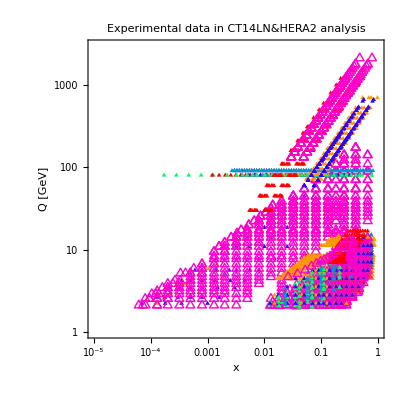

```mathematica
(*legend title set*)
PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

(*marker set 1*)
Markdft=Graphics`PlotMarkers[];

PDISNCmarker={Markdft[[4,1]],8};
NDISCCmarker={Markdft[[9,1]],15};
PDISNCCCmarker={Markdft[[4,1]],8};
PVBPZmarker={Markdft[[4,1]],8};
PVBPWmarker={Markdft[[4,1]],8};
PJPmarker={Markdft[[4,1]],8};

(*marker color set 1*)
PDISNCcolor=colorset["R"][[7]];
NDISCCcolor=colorset["R"][[3]];
PDISNCCCcolor=colorset["R"][[4]];
PVBPZcolor=colorset["B"][[1]];
PVBPWcolor=colorset["B"][[4]];
PJPcolor=colorset["G"][[1]];


lgd={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle};
(*marker set*)
myMarker={PDISNCmarker,NDISCCmarker,PDISNCCCmarker,PVBPZmarker,PVBPWmarker,PJPmarker};
marknorm=0.7;
myMarker=Table[{myMarker[[i,1]],marknorm*myMarker[[i,2]]},{i,1,Length[myMarker]}];

(*marker color set*)
myplotstyle={PDISNCcolor,NDISCCcolor,PDISNCCCcolor,PVBPZcolor,PVBPWcolor,PJPcolor};

title="Experimental data in CT14LN&HERA2 analysis";
xtitle="x";
ytitle="Q [GeV]";
{minx,maxx}={0.00001,1};
{miny,maxy}={1,3000};
xyrange={minx,maxx,miny,maxy};


Markersize=5;


lgdpos={0.225,0.725};


PDFloglogplot[tmpDISdataf1,myMarker,myplotstyle,title,xtitle,ytitle,xyrange,lgd,lgdpos]
```

```mathematica
Plotsetting=
<|
"imgsize"-> "none",
"title"-> "none",
"xtitle"->  "none",
"ytitle"->  "none",
"lgdlabel"->  "none",
"xrange"->  "none",
"yrange"->  "none",
"epilog"->  "none",
"titlesize"->  "none",
"xtitlesize"->  "none",
"ytitlesize"->  "none",
"lgdlabelsize"->  "none",
"ticklablesize"->  "none",
(*for plot 1*)
"plotstyle"->  "none",
"marker"->  "none"
|>
```

<|imgsize→none,title→none,xtitle→none,ytitle→none,lgdlabel→none,xrange→none,yrange→none,epilog→none,titlesize→none,xtitlesize→none,ytitlesize→none,lgdlabelsize→none,ticklablesize→none,plotstyle→none,marker→none|>

```mathematica
(*
exptlist, ex: {101,201,514}
plottype, 1, 2, 3
obs
*)



(*
setplotsetting[dataclassin_,exptlistin_,expttypein_,plottypein_,obsAtypein_,obsBtypein_]:=
Module[{dataclass=dataclassin,exptlist=exptlistin,expttype=expttypein,plottype=plottypein,myplotsetting,
imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,
PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle,hDISNCtitle,hDISCCtitle,hVBPZtitle,
Markdft,Psize,Nsize,hsize,myMarker,marknorm,myplotstyle,
PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker,
PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor},
(*declare a plot setting class*)
myplotsetting=Plotsetting;

(*declare*)
title="none";
lgdlabel="none";
epilog="none";
(*****************)
(*general setting*)
(*****************)
imgsize={{600},{600}};

xtitle="x";
ytitle="μ [GeV]";
xrange={0.000001,1.0};
yrange={1,1200};

titlesize=24;
xtitlesize=18;
ytitlesize=18;
lgdlabelsize=12;
ticklablesize=18;
(*****************)
(*for plot1 general setting*)
(*****************)
(*legend title set*)
PDISNCtitle="DIS NC (𝓅ℓ → ℓX)";
NDISCCtitle="DIS CC (νN → ℓX)";
PDISNCCCtitle="DIS NC&CC (𝓅ℓ → ℓX/νX)";
PVBPZtitle="VBP Z/γ^* (𝓅𝓅/𝓅𝓅̄ → ℓ^+ℓ^-X)";
PVBPWtitle="VBP ℓ asym (𝓅𝓅/𝓅𝓅̄ → ℓνX)";
PJPtitle="𝓅𝓅/𝓅𝓅̄ → 𝒿X";

hDISNCtitle="DIS NC (𝓅ℓ/dℓ → ℓX)";
hDISCCtitle="DIS CC (νFe → ℓX)";
hVBPZtitle="VBP Z/γ^* (𝓅Cu → ℓ^+ℓ^-X)";
(*marker set 1*)

Markdft=Graphics`PlotMarkers[];

Psize=8;
Nsize=15;
hsize=12;
PDISNCmarker={Markdft[[4,1]],Psize};
hDISNCmarker={"×",hsize};
NDISCCmarker={Markdft[[9,1]],Nsize};
hDISCCmarker={"×",hsize};
PDISNCCCmarker={Markdft[[4,1]],Psize};
(*PVBPWmarker=Markdft[[2]];*)
PVBPZmarker={Markdft[[4,1]],Psize};
hVBPZmarker={"×",hsize};
PVBPWmarker={Markdft[[4,1]],Psize};
PJPmarker={Markdft[[4,1]],Psize};

(*marker color set 1*)
PDISNCcolor=colorset["Brown"][[4]];
hDISNCcolor=colorset["Gray"][[4]];
NDISCCcolor=colorset["R"][[7]];
hDISCCcolor=colorset["R"][[3]];
PDISNCCCcolor=colorset["R"][[4]];
(*
PVBPWcolor=Blue;
*)
PVBPZcolor=colorset["B"][[4]];
hVBPZcolor=colorset["B"][[3]];
PVBPWcolor=colorset["B"][[1]];
PJPcolor=colorset["G"][[1]];

(*legend set*)
(*lgd={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};*)
(*marker set*)
myMarker={PDISNCmarker,hDISNCmarker,NDISCCmarker,hDISCCmarker,PDISNCCCmarker,PVBPZmarker,hVBPZmarker,PVBPWmarker,PJPmarker};
marknorm=0.7;
myMarker=Table[{myMarker[[i,1]],marknorm*myMarker[[i,2]]},{i,1,Length[myMarker]}];

(*marker color set*)
myplotstyle={PDISNCcolor,hDISNCcolor,NDISCCcolor,hDISCCcolor,PDISNCCCcolor,PVBPZcolor,hVBPZcolor,PVBPWcolor,PJPcolor};


(*****************)
(*specific setting for various plots*)
(*****************)
(*plot 1*)
If[
plottype==1,
If[
expttype=="single",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n expt id: "<>exptlist;(*dataclass[[1,1]] is [[expt,flavour]], need modify it later by variable rather than number*)
(*legend set*)
lgdlabel={dataclass[[1,1]][["exptinfo","exptname"]]};
];

If[
expttype=="multi",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n expt id: "<>exptlist;
(*legend set*)
lgdlabel=Table[dataclass[[1,1]][["exptinfo","exptname"]],{iexpt,1,Length[dataclass]}];
];

If[
expttype=="All",
title="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>" analysis \n(heavy nucleus collision included)";
(*legend set*)
lgdlabel={PDISNCtitle,hDISNCtitle,NDISCCtitle,hDISCCtitle,PDISNCCCtitle,PVBPZtitle,hVBPZtitle,PVBPWtitle,PJPtitle};

];
(*
If[
expttype=="ByProcess",
myplotsetting[["title"]]="Experimental data in "<>dataclass[["PDFinfo","PDFname"]]<>"analysis \n(heavy nucleus collision included)";
];
*)

If[
expttype=="ProtonNeutron",
myplotsetting[["title"]]="Experimental data in "<>dataclass[[1,1]][["PDFinfo","PDFname"]]<>"analysis \n";
(*legend set*)
lgdlabel={PDISNCtitle,NDISCCtitle,PDISNCCCtitle,PVBPZtitle,PVBPWtitle,PJPtitle};
];
];
(*plot 2*)

(*plot 3*)

(*read setting to class and output the class*)
myplotsetting[["imgsize"]]=imgsize;
myplotsetting[["title"]]=title;
myplotsetting[["xtitle"]]=xtitle;
myplotsetting[["ytitle"]]=ytitle;
myplotsetting[["lgdlabel"]]=lgdlabel;
myplotsetting[["xrange"]]=xrange;
myplotsetting[["yrange"]]=yrange;
myplotsetting[["epilog"]]=epilog;
myplotsetting[["titlesize"]]=titlesize;
myplotsetting[["xtitlesize"]]=xtitlesize;
myplotsetting[["ytitlesize"]]=ytitlesize;
myplotsetting[["lgdlabelsize"]]=lgdlabelsize;
myplotsetting[["ticklablesize"]]=ticklablesize;

myplotsetting[["plotstyle"]]=myplotstyle;
myplotsetting[["marker"]]=myMarker;

myplotsetting

]
*)
```

```mathematica
Plotsetting
Keys[Plotsetting]
```

<|imgsize→none,title→none,xtitle→none,ytitle→none,lgdlabel→none,xrange→none,yrange→none,epilog→none,titlesize→none,xtitlesize→none,ytitlesize→none,lgdlabelsize→none,ticklablesize→none,plotstyle→none,marker→none|>

{imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize,plotstyle,marker}

```mathematica
{"imgsize","title","xtitle","ytitle","lgdlabel","xrange","yrange","epilog","titlesize","xtitlesize","ytitlesize","lgdlabelsize","ticklablesize"}
```

{imgsize,title,xtitle,ytitle,lgdlabel,xrange,yrange,epilog,titlesize,xtitlesize,ytitlesize,lgdlabelsize,ticklablesize}

```mathematica
setplotsetting[corrfxQdtaobsclass,{101,201,514},"All",plottypein_,"test","test"]
```

<|imgsize→{{700},{700}},title→none,xtitle→x,ytitle→μ [GeV],lgdlabel→none,xrange→{1.×10^-6,1.},yrange→{1,1200},epilog→none,titlesize→24,xtitlesize→18,ytitlesize→18,lgdlabelsize→12,ticklablesize→18,plotstyle→{RGBColor[0.6, 0.2, 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[1., 0., 0.],RGBColor[1., 0., 0.8],RGBColor[1., 0.6, 0.],RGBColor[0., 0.6, 0.8],RGBColor[0., 0.8, 1.],RGBColor[0.2, 0., 1.],RGBColor[0., 1., 0.4]},marker→{{▲,5.6},{×,8.4},{△,10.5},{×,8.4},{▲,5.6},{▲,5.6},{×,8.4},{▲,5.6},{▲,5.6}}|>

```mathematica
Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
(*set input data*)
tmpDISdataf1=Table[Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,6]],{1,2} ],{iexpt,1,Length[corrfxQdtaobsclass]}];
tmpDISdataf1=Table[tmpDISdataf1[[iexpt]][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclass]}];
(*read setting to class and output the class*)

corrfxQdtaobsclass[[1,1]][["PDFinfo"]]
myplotsetting=setplotsetting[corrfxQdtaobsclass,{101,201,514},"multi",1,"test","test"]
imgsize=myplotsetting[["imgsize"]];
title=myplotsetting[["title"]];
xtitle=myplotsetting[["xtitle"]];
ytitle=myplotsetting[["ytitle"]];
lgdlabel=myplotsetting[["lgdlabel"]];
xrange=myplotsetting[["xrange"]];
yrange=myplotsetting[["yrange"]];
epilog=myplotsetting[["epilog"]];
titlesize=myplotsetting[["titlesize"]];
xtitlesize=myplotsetting[["xtitlesize"]];
ytitlesize=myplotsetting[["ytitlesize"]];
lgdlabelsize=myplotsetting[["lgdlabelsize"]];
ticklablesize=myplotsetting[["ticklablesize"]];
myplotstyle=myplotsetting[["plotstyle"]];
myMarker=myplotsetting[["marker"]];
```

<|PDFname→CT14NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>

<|imgsize→{{700},{700}},title→Experimental data in CT14NNLO analysis 
 expt id: {101, 201, 514},xtitle→x,ytitle→μ [GeV],lgdlabel→{BcdF2pCor,NmcX0pCor,H1FL10,Hn1X0c,Hn+9900x0b,NuTvNuChXN,NuTvNbChXN,HERA1X0,e866ppxf,ZyD02a,ZyCDF2,LHCb7Wasy1,CMS7Masy2,CMS7Easy,cdfLasy,cdfLasy2,d02Masy1,d02Easy5,ATL7jtR6,CMS7jtR7,cdf2jtCor2,d02jtCor2,BcdF2dCor,NmcRatCor,cdhswf2,cdhswf3,ccfrf2.mi,ccfrf3.md,CcfrNuChXN,CcfrNbChXN,e605,e866f},xrange→{1.×10^-6,1.},yrange→{1,1200},epilog→none,titlesize→24,xtitlesize→18,ytitlesize→18,lgdlabelsize→12,ticklablesize→18,plotstyle→{RGBColor[0.6, 0.2, 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[1., 0., 0.],RGBColor[1., 0., 0.8],RGBColor[1., 0.6, 0.],RGBColor[0., 0.6, 0.8],RGBColor[0., 0.8, 1.],RGBColor[0.2, 0., 1.],RGBColor[0., 1., 0.4]},marker→{{▲,5.6},{×,8.4},{△,10.5},{×,8.4},{▲,5.6},{▲,5.6},{×,8.4},{▲,5.6},{▲,5.6}}|>

{1.×10^-6,1.,1,1200}

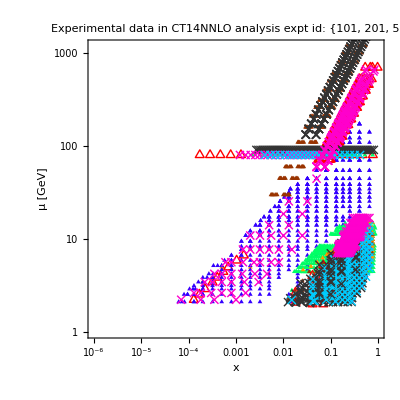

```mathematica
lgdpos={0.225,0.725};
xyrange={xrange,yrange}//Flatten
PDFloglogplot[tmpDISdataf1,myMarker,myplotstyle,title,xtitle,ytitle,xyrange,lgdlabel,lgdpos]
```

```mathematica
lgdlabel
myMarker
myplotstyle
```

{BcdF2pCor,NmcX0pCor,H1FL10,Hn1X0c,Hn+9900x0b,NuTvNuChXN,NuTvNbChXN,HERA1X0,e866ppxf,ZyD02a,ZyCDF2,LHCb7Wasy1,CMS7Masy2,CMS7Easy,cdfLasy,cdfLasy2,d02Masy1,d02Easy5,ATL7jtR6,CMS7jtR7,cdf2jtCor2,d02jtCor2,BcdF2dCor,NmcRatCor,cdhswf2,cdhswf3,ccfrf2.mi,ccfrf3.md,CcfrNuChXN,CcfrNbChXN,e605,e866f}

{{▲,5.6},{×,8.4},{△,10.5},{×,8.4},{▲,5.6},{▲,5.6},{×,8.4},{▲,5.6},{▲,5.6}}

{RGBColor[0.6, 0.2, 0.],RGBColor[0.2, 0.2, 0.2],RGBColor[1., 0., 0.],RGBColor[1., 0., 0.8],RGBColor[1., 0.6, 0.],RGBColor[0., 0.6, 0.8],RGBColor[0., 0.8, 1.],RGBColor[0.2, 0., 1.],RGBColor[0., 1., 0.4]}

```mathematica
flavour=-5;
SMmode=1;
{procs,expids}=toprocexptidlist[exptlist];
processdataplotsmultiexp2[corrfxQdtaobsclass,dRcorrfxQdtaobsclass,deltaRclass,(*pdfdatain_,*)myPDFsetDir<>"whatever",(*PDFDataDirin_,CorrDataDirin_,*)datalistFile,procs,expids,flavour,SMmode][[5]]
```

/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica

```mathematica
plot1data=Table[Datamethods[["take"]][corrfxQdtaobsclass[[iexpt,flavour+6]],{1,2}][["data"]],{iexpt,1,Length[corrfxQdtaobsclass]}];
```

## tutorial: A. chapter “read package” includes packages and some global variables; title “Correlation plots project” includes all functions in this program. run them to initialize under title “Correlation plots project (implementation part)”: B. section “inteprete and save pdf data into files” read .dta files and .pds files then save f(x,Q, flavour) information for (x,Q) of experiments you input 1. set .dta file path of the PDFset you use by myPDFsetDir ex: CT14NNLODir=”/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/”; myPDFsetDir=CT14NNLODir 2. set PDFDataDir which store data of f(x,Q,flavour=0~5 ) PDFDataDir=”/home/botingw/code/pdf_correlation/data/sameptcorr/”<>”pdfxQnew/”; 3. set datalistFile to get information of experiments in datalist (it seems you need to set it as absolute path) ex: datalistFile=”/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica”; 5. set exptlist for experiments you want to show, input exptid printed by “printprocessbyPDFset”: exptlist={101,102,103} 6. run all subsections until subsection “save f(x,Q) data into files” to save parton density function data C. title “read f(x,Q) and make plots of correlation of experiments & f(x,Q), default mode: Corr(residue, f(x,Q,flavour)) ” read f(x,Q,flavour) of experiments you choose and .dta files then make plots of correlation, dr*correlation and deltaR 1. set .dta file path of the PDFset you use by myPDFsetDir ex: CT14NNLODir=”/home/botingw/code/pdf_correlation/dta_file/CT14NNLO/”; myPDFsetDir=CT14NNLODir 2. set PDFDataDir which store data of f(x,Q,flavour=0~5 ) PDFDataDir=”/home/botingw/code/pdf_correlation/data/sameptcorr/”<>”pdfxQnew/”; 3. set datalistFile to get information of experiments in datalist (it seems you need to set it as absolute path) ex: datalistFile=”/home/botingw/code/pdf_correlation/exp_catogory/dat16lisformathematica”; 4. run function “printprocessbyPDFset” to see the info of experiments you can use ex: printprocessbyPDFset[myPDFsetdtafile,datalistFile] 5. set exptlist for experiments you want to show, input exptid printed by “printprocessbyPDFset”: exptlist={101,102,103} 6. run subsection “set input arguments” 7. run next subsection and next... 8. when you run the last subsection “manipulate”, you will get the result